```mathematica
(*pixel diff data*)
directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/mlxfilt data/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,26}];
mlfilt=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/mlxunfilt data/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,26}];
mlunfilt=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manual/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,26}];
manual=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manxfilt data/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,26}];
manfilt=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manxunfilt data/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,26}];
manunfilt=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/filtxunfilt data/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,26}];
funfilt=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/filtxfilt data/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,26}];
filfilt=Import[#,"CSV"]&/@fileNames;

(*mlfilt=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/mlxfilt data/pixel_diff/"];
mlunfilt=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/mlxunfilt data/pixel_diff/"];
manual=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manual/pixel_diff/"];
manfilt=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manxfilt data/pixel_diff/"];
manunfilt=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manxunfilt data/pixel_diff/"];
funfilt=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/filtxunfilt data/pixel_diff/"];
filfilt=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/filtxfilt data/pixel_diff/"];*)
```

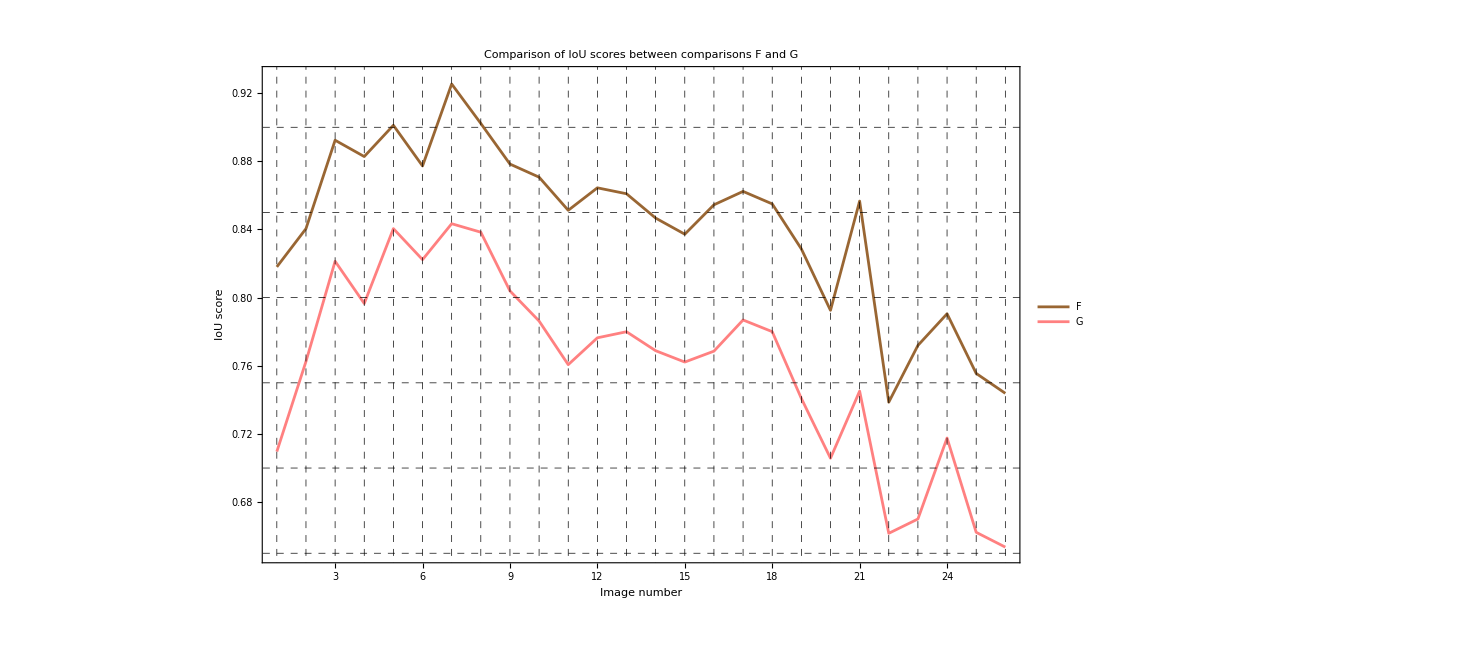

```mathematica
(*K ML x A filt vs K ML x A unfilt*)y=ListLinePlot[Flatten[mlfilt],PlotStyle->Pink,Frame->True,AxesLabel->{Style["Image number",Black,Bold],Style["Pixel Difference",Black,Bold]},PlotLegends->{Style["G",Black,18]}];
z=ListLinePlot[Flatten[mlunfilt],PlotStyle->Brown,Frame->True,AxesLabel->{None,Style["IoU score",Black,Bold]},PlotLegends->{Style["F",Black,18]}];
Show[z,y,Frame->True,FrameLabel->{Style["Image number",Black,Bold,22],Style["IoU score",Black,Bold,22]},PlotLabel->Style["Comparison of IoU scores between comparisons F and G",Black,Bold,22],PlotRange->{0.65,0.93},Background->White,LabelStyle->Directive[Bold, Black,18],PlotTheme->"Scientific",GridLines->{Range[0, 26, 1],Range[0.65,0.95,0.05]},GridLinesStyle->Directive[Black,Dashed]]
```

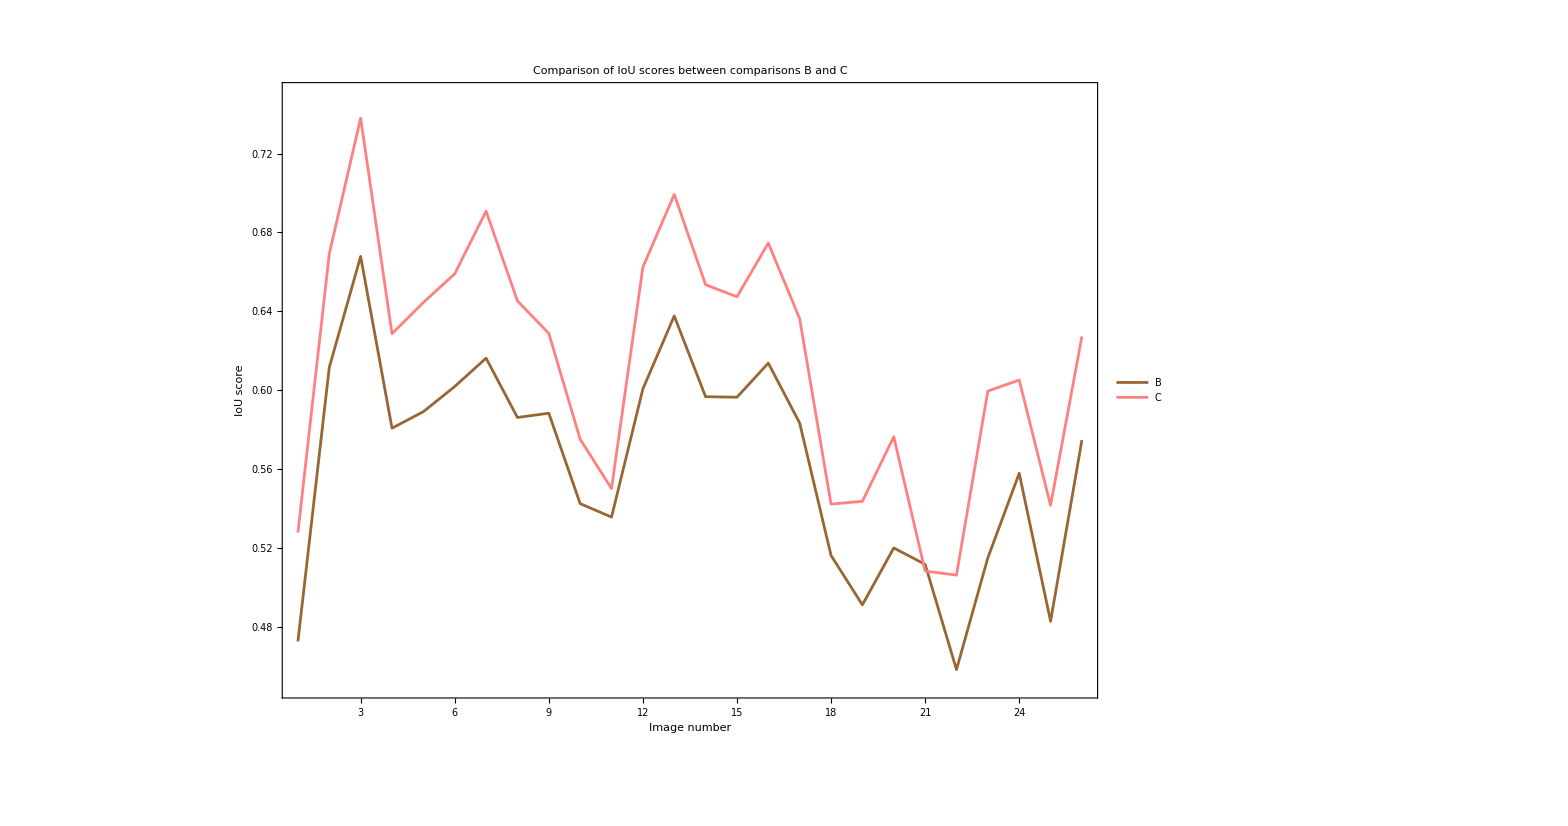

```mathematica
z=ListLinePlot[Flatten[manunfilt],PlotStyle->Brown,Frame->True,AxesLabel->{None,Style["Pixel Difference",Black,Bold]},PlotLegends->{Style["B",Black,18]}];
y=ListLinePlot[Flatten[manfilt],PlotStyle->Pink,Frame->True,AxesLabel->{None,Style["Pixel Difference",Black,Bold]},PlotLegends->{Style["C",Black,18]}];

Show[z,y,Frame->True,FrameLabel->{Style["Image number",Black,Bold,15],Style["IoU score",Black,Bold,18]},PlotLabel->Style["Comparison of IoU scores between comparisons B and C",Black,Bold],PlotRange->{0.45,0.75},Background->White, LabelStyle->Directive[Bold, Black,18]]
```

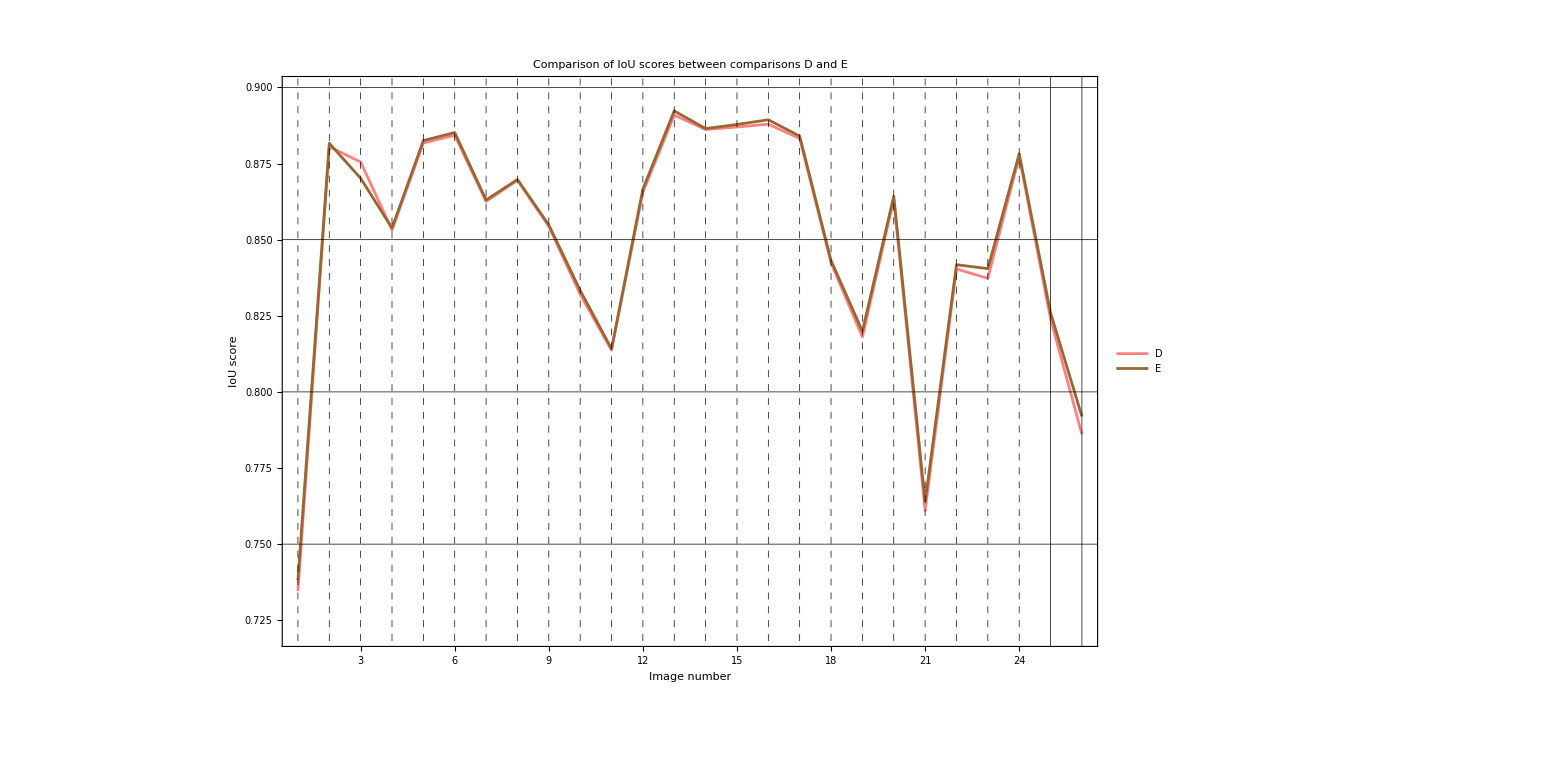

```mathematica
(*filtxunfilt vs filtxfilt*)
y=ListLinePlot[Flatten[funfilt],PlotStyle->Pink,Frame->True,AxesLabel->{None,Style["Pixel Difference",Black,Bold]},PlotLegends->{Style["D",Black,18]}];
z=ListLinePlot[Flatten[filfilt],PlotStyle->Brown,Frame->True,AxesLabel->{None,Style["Pixel Difference",Black,Bold]},PlotLegends->{Style["E",Black,18]}];
Show[y,z,Frame->True,FrameLabel->{Style["Image number",Black,Bold,22],Style["IoU score",Black,Bold,22]},PlotLabel->Style["Comparison of IoU scores between comparisons D and E",Black,Bold],PlotRange->{0.72,0.90},Background->White,LabelStyle->Directive[Bold, Black,22],PlotTheme->"Scientific",GridLines->{Range[0, 26, 1],Range[0.70,0.90,0.05]},GridLinesStyle->Directive[Black,Dashed]]
```

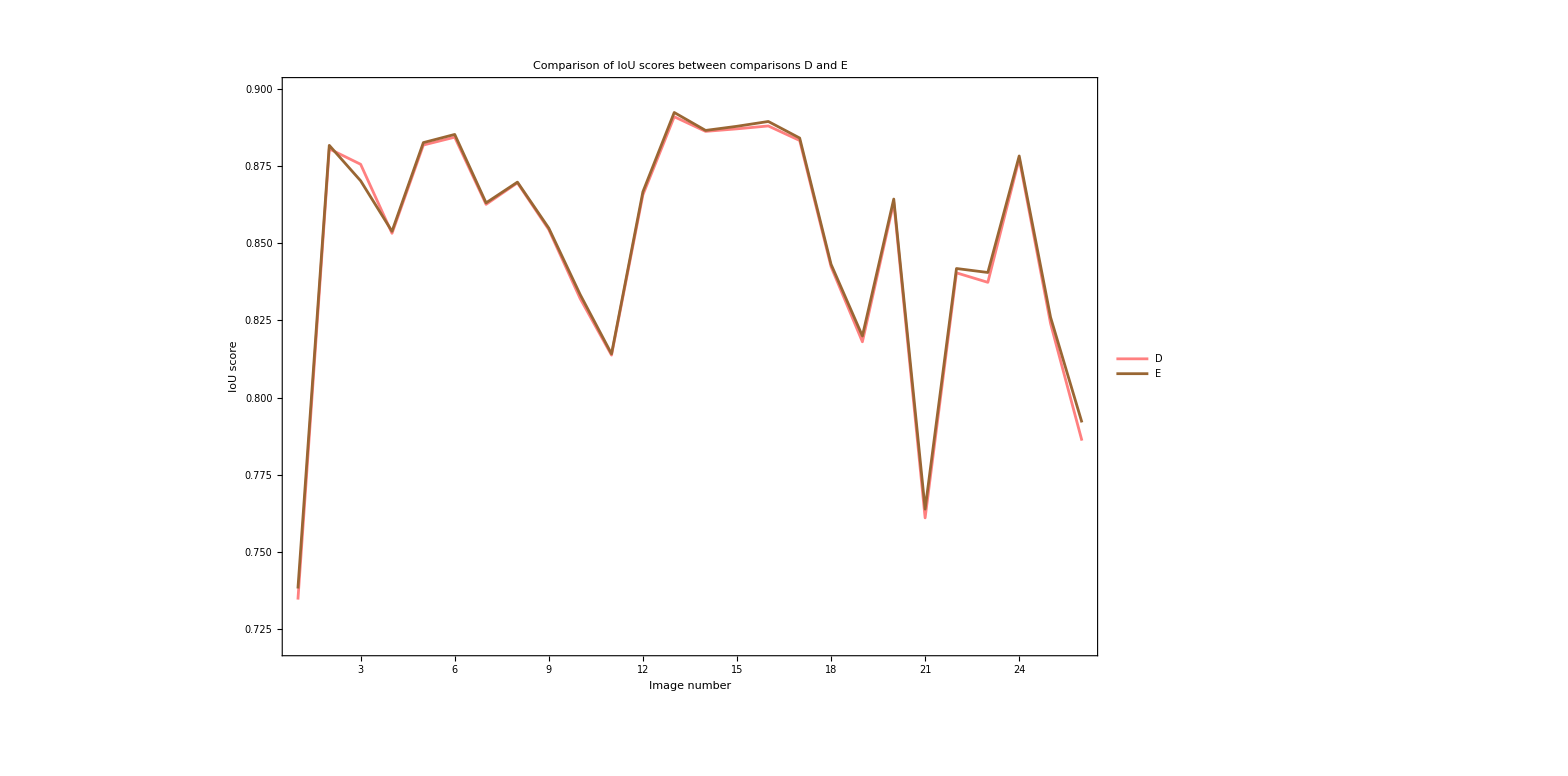

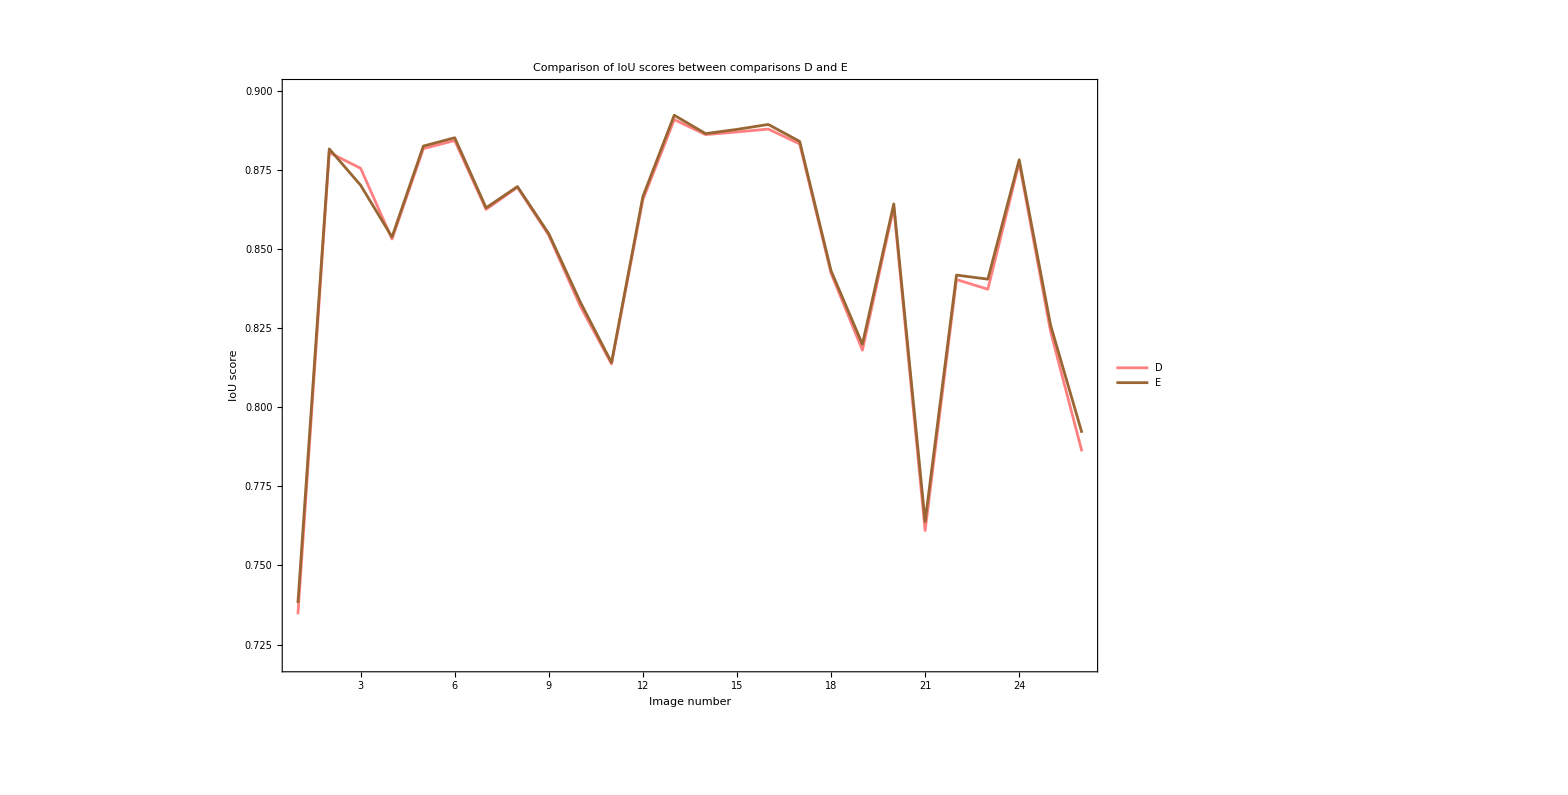

```mathematica
ListLinePlot[Flatten[manual],PlotStyle->"DarkGreen",Frame->True,FrameLabel->{Style["Image number",Black,Bold,15],Style["Pixel Difference",Black,Bold,15]},PlotLabel->Style["Plot of Manual pixel differences",Black,Bold],PlotRange->Automatic,Background->White, PlotLegends->{"Manual"},LabelStyle->Directive[Bold, Black,12]]
```

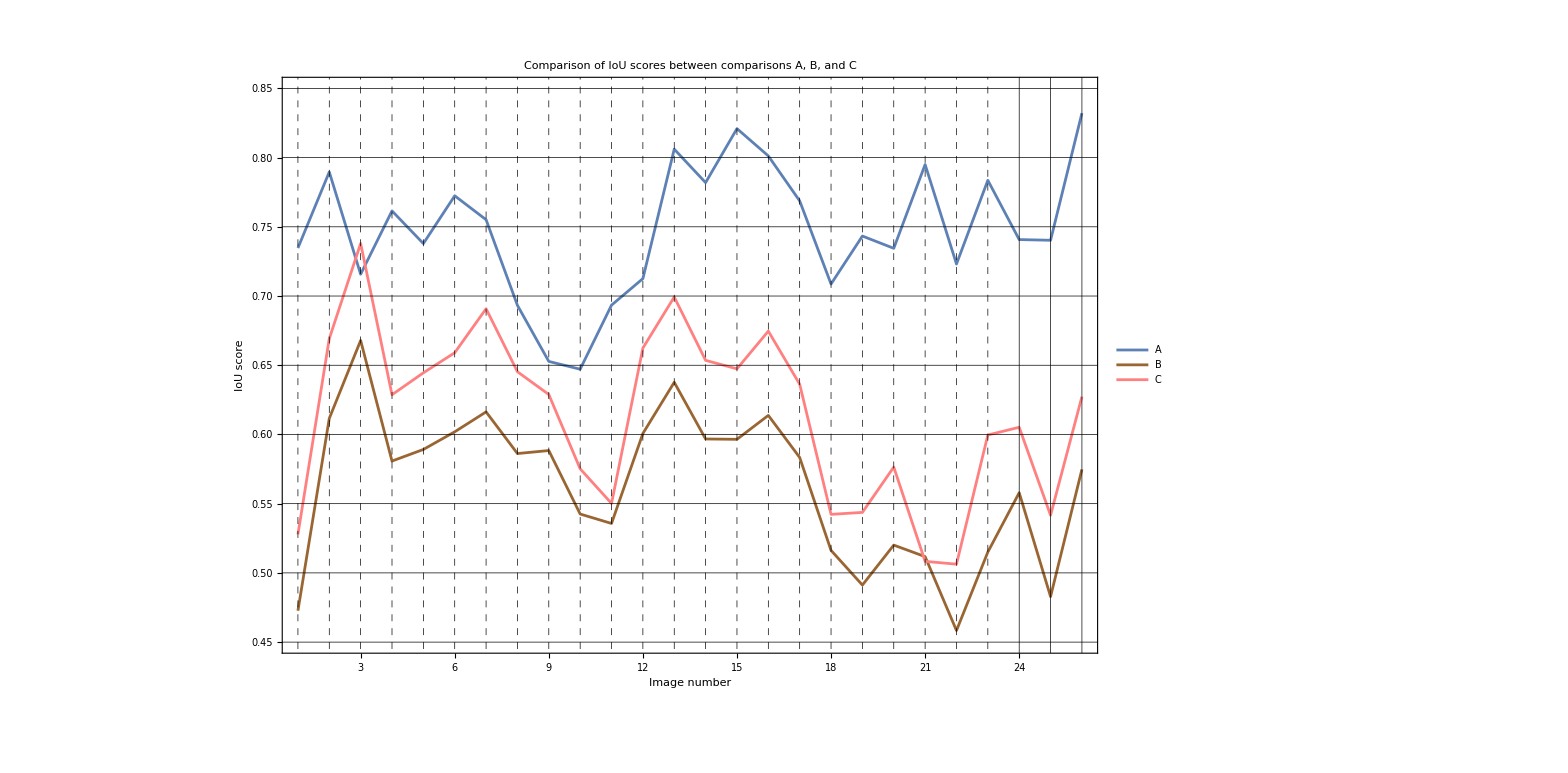

```mathematica
y=ListLinePlot[Flatten[manfilt],PlotStyle->Pink,Frame->True,AxesLabel->{None,Style["Pixel Difference",Black,Bold]},PlotLegends->{Style["C",Black,18, Bold]}];
z=ListLinePlot[Flatten[manunfilt],PlotStyle->Brown,Frame->True,AxesLabel->{None,Style["Pixel Difference",Black,Bold]},PlotLegends->{Style["B",Black,18, Bold]}];
m=ListLinePlot[Flatten[manual],PlotStyle->DarkGreen,Frame->True,FrameLabel->{Style["Image number",Black,Bold,15],Style["Pixel Difference",Black,Bold,18]},PlotLabel->Style["Plot of Manual pixel differences",Black,Bold],PlotRange->Automatic,Background->White,PlotLegends->{"A"},LabelStyle->Directive[Bold,Black,18]];

verticalLines={{10,Directive[Black,Dashed]},{20,Directive[Black,Dashed]}};

Show[m,z,y,Frame->True,FrameLabel->{Style["Image number",Black,Bold,22],Style["IoU score",Black,Bold,22]},PlotLabel->Style["Comparison of IoU scores between comparisons A, B, and C",Black,Bold],PlotRange->{0.45,0.85},Background->White,LabelStyle->Directive[Bold,Black,22], PlotTheme->"Scientific",GridLines->{Range[0, 26, 1],Range[0.45,0.85,0.05]},GridLinesStyle->Directive[Black,Dashed]]
```

```mathematica
(*flatten data sets*)
a=Flatten[mlunfilt];
b=Flatten[mlfilt];
c=Flatten[manual];
d=Flatten[manfilt];
e=Flatten[manunfilt];
f=Flatten[funfilt];
g=Flatten[filfilt];
```

```mathematica
descriptiveStats={{Mean[#],Median[#],StandardDeviation[#],Min[#],Max[#]}&/@{c,e,d,f,g,a,b}}
```

{{{0.747932,0.742047,0.0475338,0.64713,0.832087},{0.563467,0.582084,0.054076,0.458375,0.667883},{0.614692,0.628781,0.0626484,0.506298,0.737974},{0.849724,0.862911,0.0406814,0.734579,0.890927},{0.850886,0.863656,0.0396827,0.738169,0.892302},{0.842297,0.854755,0.0498696,0.738658,0.925385},{0.760215,0.768726,0.0564377,0.653578,0.843384}}}

```mathematica
(*coeff of variance pixel diff*)
CV[std_,mean_]:=(StandardDeviation[std]/Mean[mean])*100
CV[c,c]
CV[d,d]
CV[e,e]
CV[f,f]
CV[g,g]
CV[a,a]
CV[b,b]
```

6.35535

10.1918

9.59701

4.7876

4.66369

5.92066

7.42392

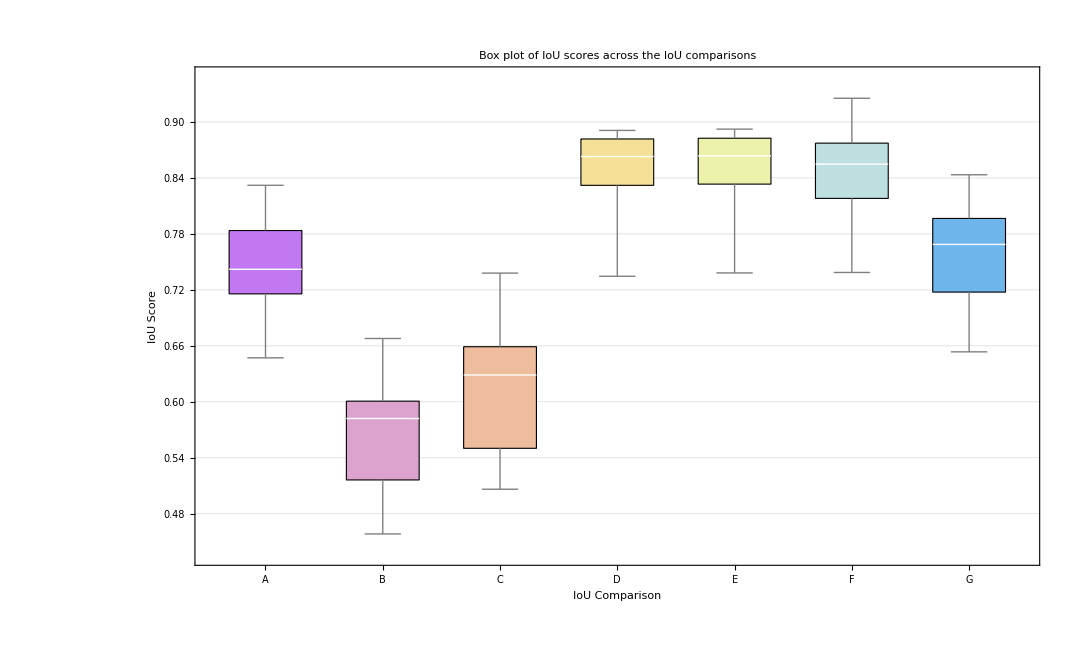

```mathematica
(*ChartLegends->{"a","b","c","d","e","f","g"}*)

BoxWhiskerChart[{c,e,d, f,g,a,b},ChartStyle->{EdgeForm[Black],"Pastel"}, ChartLabels->{"A","B", "C", "D", "E", "F", "G",Style[Black, Bold]}, Background->White,  PlotTheme->"Detailed", FrameLabel->{Style["IoU Comparison",Black,Bold,22],Style["IoU Score",Black,Bold,22]}, LabelStyle->Directive[Bold, Black,22], PlotLabel->Style["Box plot of IoU scores across the IoU comparisons", Black, 22]]
```

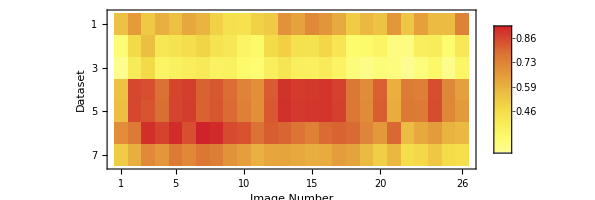

```mathematica
MatrixPlot[{c,d,e,f,g,a,b},ColorFunction->"TemperatureMap", PlotLegends->Automatic, Background->White,LabelStyle->Directive[Bold, Black,18], FrameTicks->All, FrameLabel->{"Dataset", "Image Number"}]
```

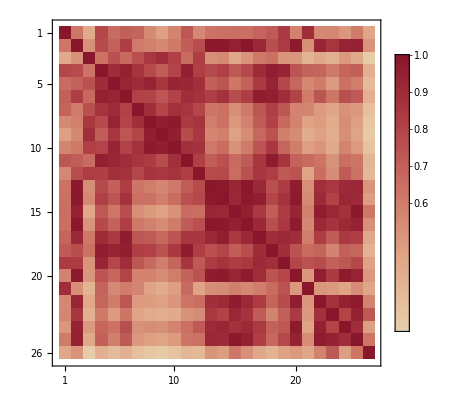

```mathematica
correlationMatrix=Correlation[{c,e,d, f,g,a,b}];

(*Visualize the correlation matrix as a heatmap*)
MatrixPlot[correlationMatrix,ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

```mathematica
pearsonCoefficient=Correlation[a,b]
pearsonCoefficient=Correlation[d,e]
pearsonCoefficient=Correlation[f,g]
pearsonCoefficient=Correlation[g,c]
Correlation[c,a]
Correlation[c,b]
Correlation[c,d]
Correlation[c,e]
Correlation[c,f]
Correlation[c,g]
Correlation[a,b]
Correlation[d,a]
Correlation[e,a]
Correlation[f,a]
Correlation[g,a]
Correlation[c,a]
Correlation[c,a]
Correlation[c,a]
```

0.976827

0.96313

0.999278

0.100327

-0.25557

-0.265694

0.249331

0.211891

0.0806567

0.100327

0.976827

0.526775

0.625723

0.362792

0.346452

-0.25557

-0.25557

-0.25557

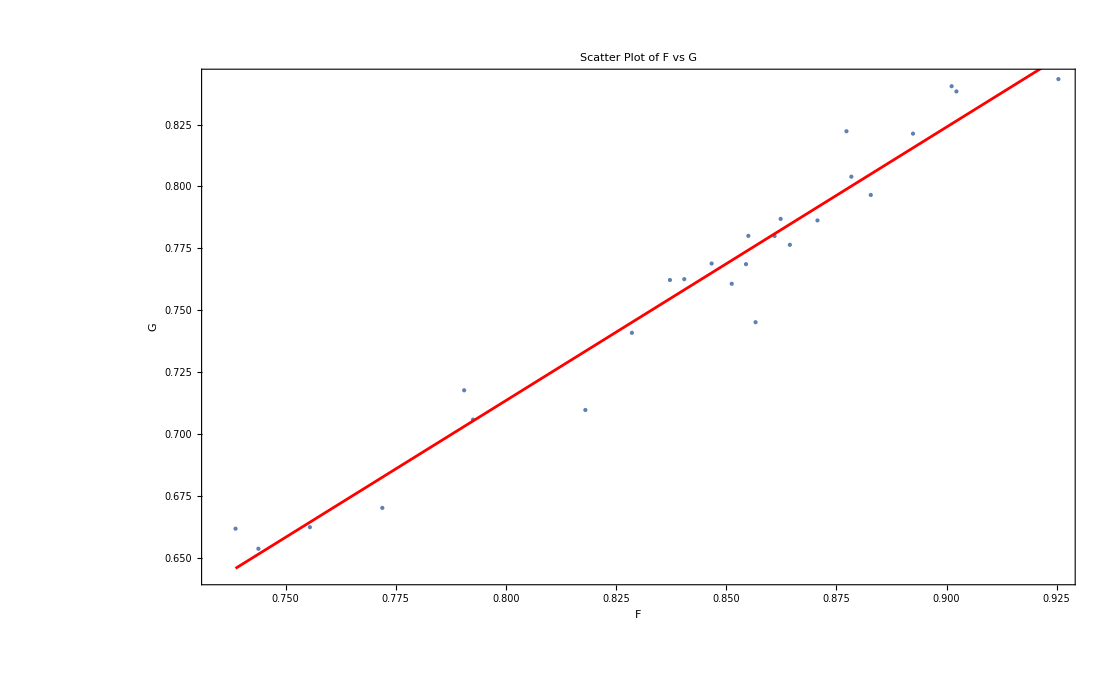

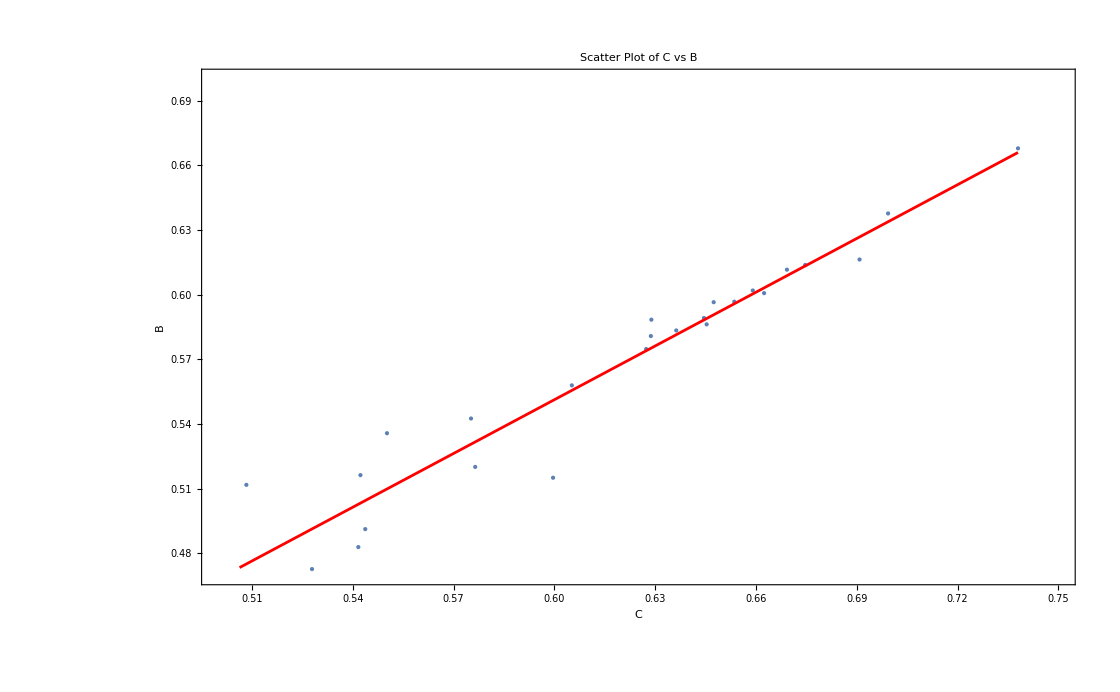

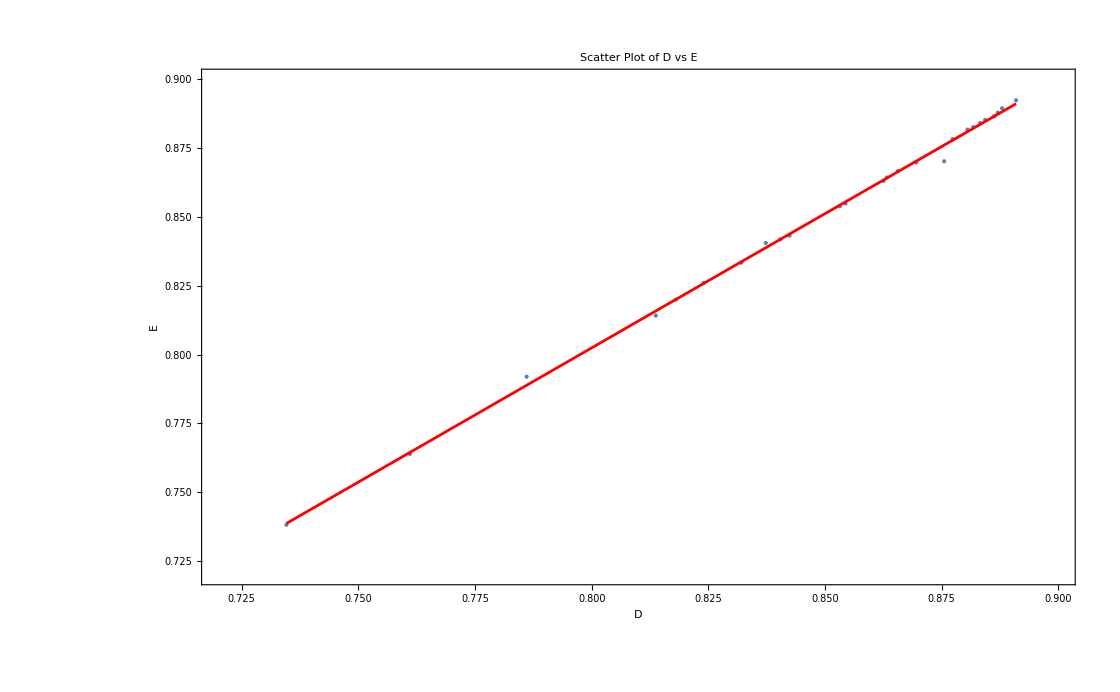

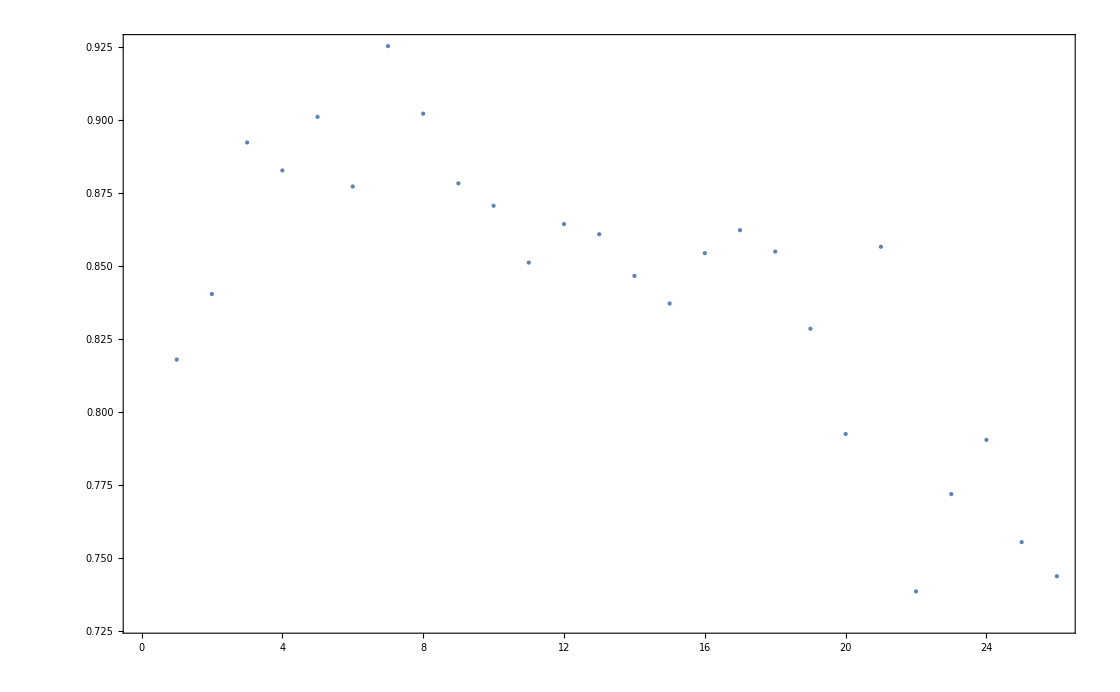

```mathematica
(*Visualize the relationship between the datasets*)
{m,p}={Total[(a-Mean[a]) (b-Mean[b])]/Total[(a-Mean[a])^2],Mean[b]-(Total[(a-Mean[a]) (b-Mean[b])]/Total[(a-Mean[a])^2])*Mean[a]};

(*Create scatter plot with trend line*)
Show[ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"F","G"},PlotLabel->"Scatter Plot of F vs G", Background->White],Plot[m x+p,{x,Min[a],Max[a]},PlotStyle->Directive[Red,Medium],PlotRange->All], FrameLabel->{Style["F",Black,Bold,18],Style["G",Black,Bold,18]},LabelStyle->Directive[Bold, Black,18]]
(************************************************************************************************************************************************************)

{m,p}={Total[(d-Mean[d]) (e-Mean[e])]/Total[(d-Mean[d])^2],Mean[e]-(Total[(d-Mean[d]) (e-Mean[e])]/Total[(d-Mean[d])^2])*Mean[d]};

(*Create scatter plot with trend line*)
Show[ListPlot[Transpose[{d,e}],PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"C","B"},PlotLabel->"Scatter Plot of C vs B",Background->White,PlotRange->{{0.5,0.75},{0.47,0.70}}],Plot[m x+p,{x,Min[d],Max[d]},PlotStyle->Directive[Red,Medium]], FrameLabel->{Style["C",Black,Bold,18],Style["B",Black,Bold,18]},LabelStyle->Directive[Bold, Black,18]]

(*************************************************************************************************************************************************************)

{m,p}={Total[(f-Mean[f]) (g-Mean[g])]/Total[(f-Mean[f])^2],Mean[g]-(Total[(f-Mean[f]) (g-Mean[g])]/Total[(f-Mean[f])^2])*Mean[f]};

(*Create scatter plot with trend line*)

Show[ListPlot[Transpose[{f,g}],PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"D","E"},PlotLabel->"Scatter Plot of D vs E",Background->White,PlotRange->{{0.72,0.90},{0.72,0.90}}],Plot[m x+p,{x,Min[f],Max[f]},PlotStyle->Directive[Red,Medium]], FrameLabel->{Style["D",Black,Bold,18],Style["E",Black,Bold,18]},LabelStyle->Directive[Bold, Black,18]]
(************************************************************************************************************************************************************)

ListPlot[a,PlotStyle->PointSize[Medium],Frame->True, Background->White]
```

```mathematica
(*Histogram[a]
Histogram[b]
Histogram[c]
Histogram[d]
Histogram[e]
Histogram[f]*)
```

```mathematica
(*paired dataset ancova*)
(*Perform ANCOVA for pairs of datasets
ANCOVAResultsPairs=Table[ANCOVA[Transpose[{covariate,datasets[[i]]}],Transpose[{covariate,datasets[[j]]}]],{i,1,Length[datasets]},{j,i+1,Length[datasets]}];

(*Display ANCOVA results for each pair*)
ANCOVAResultsPairs;*)

(*t-tests*)
tTest=TTest[{a,b}]
tTest=TTest[{d,e}]
tTest=TTest[{f,g}]
```

1.05804×10^-6

0.00270788

0.917353

```mathematica
chiSquareTest=PearsonChiSquareTest[a]
chiSquareTest=PearsonChiSquareTest[b]
chiSquareTest=PearsonChiSquareTest[c]
chiSquareTest=PearsonChiSquareTest[d]
chiSquareTest=PearsonChiSquareTest[e]
chiSquareTest=PearsonChiSquareTest[f]
chiSquareTest=PearsonChiSquareTest[g]
```

0.617576

0.250851

0.306219

0.306219

0.0844381

0.00729732

0.0121386

```mathematica
(*visual stats
BoxWhiskerChart[{a,b,c,d,e,f,g}]

ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Medium]]



BarChart[{a,b,c,d,e,f,g}];

ListLinePlot[{a,b,d,e}]

Grid[Table[ListPlot[Transpose[{a,b}[[{i,j}]]]],{i,1,2},{j,1,2}]]*)
```

```mathematica
shapiroWilkTest=ShapiroWilkTest[g]
If[shapiroWilkTest>0.05,Print["Data may be normally distributed"],Print["Data may not be normally distributed"]]
```

0.00243786

Data may not be normally distributed

```mathematica
(**********************************************************************************************************************************)
```

```mathematica
(*component measurements data*)

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manual/component_measurements/";
fileNames=Table[directory<>"data_AS_"<>IntegerString[i]<>".csv",{i,1,26}];
manualAS=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/mlxunfilt data/component_measurements/";
fileNames=Table[directory<>"data_unfil_"<>IntegerString[i]<>".csv",{i,1,26}];
unfiltered=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manxfilt data/component_measurements/";
fileNames=Table[directory<>"data_fil_"<>IntegerString[i]<>".csv",{i,1,26}];
filtered=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manual/component_measurements/";
fileNames=Table[directory<>"data_KS_"<>IntegerString[i]<>".csv",{i,1,26}];
manualKS=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/mlxunfilt data/component_measurements/";
fileNames=Table[directory<>"data_ml_"<>IntegerString[i]<>".csv",{i,1,26}];
mlKS=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/filtxfilt data/component_measurements/";
fileNames=Table[directory<>"data_unfil_"<>IntegerString[i]<>".csv",{i,1,26}];
filtunfilt=Import[#,"CSV"]&/@fileNames;
```

```mathematica
(*extract area and roundness*)

filteredarea=filtered[[All,All, 4]];
unfilteredarea=unfiltered[[All,All,4]];
manualASarea=manualAS[[All,All,4]];
manualKSarea=manualKS[[All,All,4]];
mlKSarea=mlKS[[All,All,4]];
funfiltarea=filtunfilt[[All,All,4]];

filteredround=filtered[[All,All, 5]];
unfilteredround=unfiltered[[All,All,5]];
manualASround=manualAS[[All,All,5]];
manualKSround=manualKS[[All,All,5]];
mlKSround=mlKS[[All,All,5]];
funfiltround=filtunfilt[[All,All,5]];
```

```mathematica
(*Delete strings*)

filteredarea=DeleteCases[filteredarea,_String,{2}];
unfilteredarea=DeleteCases[unfilteredarea,_String,{2}];
manualASarea=DeleteCases[manualASarea,_String,{2}];
manualKSarea=DeleteCases[manualKSarea,_String,{2}];
mlKSarea=DeleteCases[mlKSarea,_String,{2}];
funfiltarea=DeleteCases[funfiltarea,_String,{2}];

filteredround=DeleteCases[filteredround,_String,{2}];
unfilteredround=DeleteCases[unfilteredround,_String,{2}];
manualASround=DeleteCases[manualASround,_String,{2}];
manualKSround=DeleteCases[manualKSround,_String,{2}];
mlKSround=DeleteCases[mlKSround,_String,{2}];
funfiltround=DeleteCases[funfiltround,_String,{2}];
```

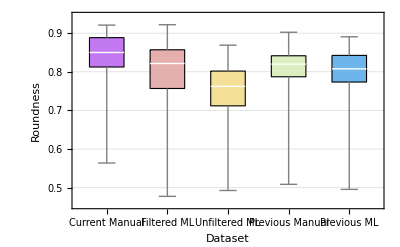

-Graphics-

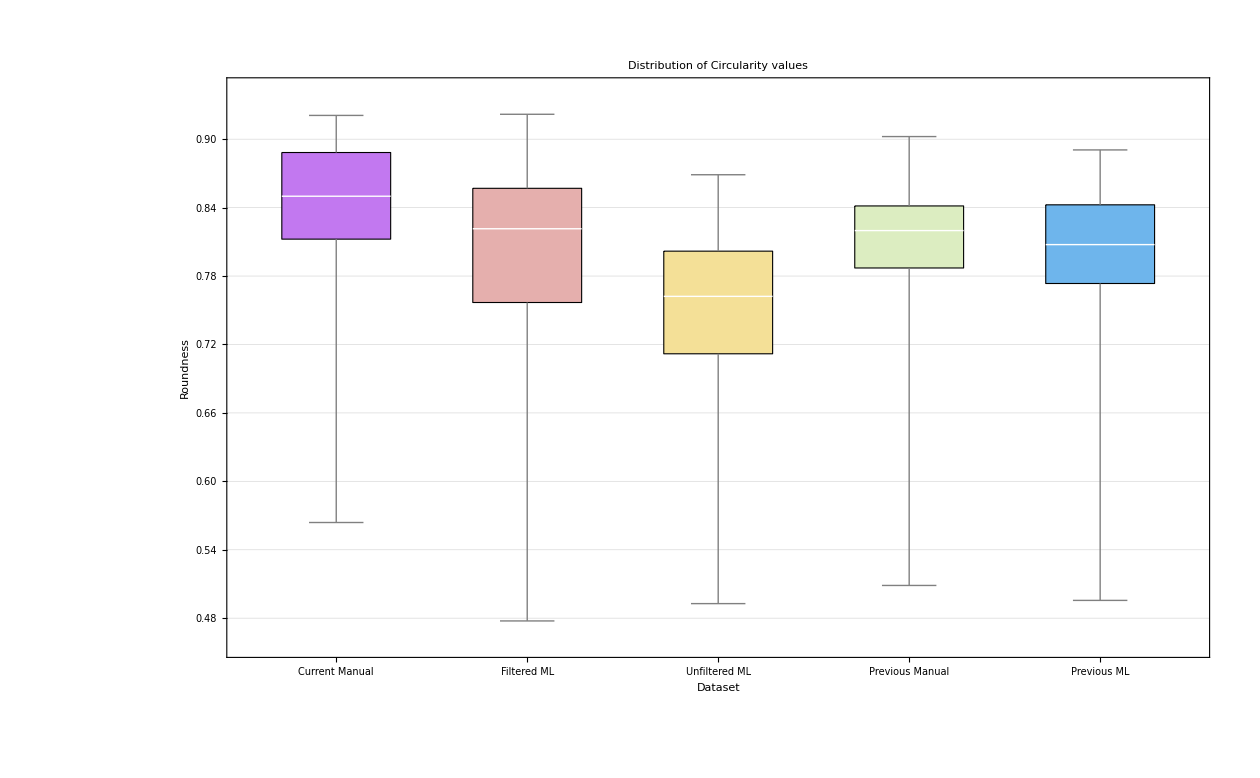

```mathematica
(*once image finalised/ use area of that particular image*)
BoxWhiskerChart[{manualASround[[12]],filteredround[[12]],unfilteredround[[12]],manualKSround[[12]],mlKSround[[12]]},ChartStyle->{EdgeForm[Black],"Pastel"},ChartLabels->{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML", Style[Black, Bold, 18]},FrameLabel->{Style["Dataset",Black,Bold,18],Style["Roundness",Black,Bold,18]},Background->White,LabelStyle->Directive[Bold, Medium],PlotTheme->"Detailed"]


BoxWhiskerChart[{manualASround[[12]],filteredround[[12]],unfilteredround[[12]],manualKSround[[12]],mlKSround[[12]]},ChartStyle->{EdgeForm[Black],"Pastel"}, ChartLabels->{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML",Style[Black, Bold]}, Background->White,  PlotTheme->"Detailed", FrameLabel->{Style["Dataset",Black,Bold,18],Style["Roundness",Black,Bold,18]}, LabelStyle->Directive[Bold, Black,18]]

BoxWhiskerChart[{manualASround[[12]],filteredround[[12]],unfilteredround[[12]],manualKSround[[12]],mlKSround[[12]]},ChartStyle->{EdgeForm[Black],"Pastel"},  Background->White,  PlotTheme->"Detailed", ChartLabels->{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML",Style[Black, Bold]},FrameLabel->{Style["Dataset",Black,Bold,18],Style["Roundness",Black,Bold,18]}, LabelStyle->Directive[Bold, Black,18], PlotLabel->Style["Distribution of Circularity values", Black, 20]]
```

```mathematica
descriptiveStats={{Mean[#],Median[#],StandardDeviation[#],Min[#],Max[#]}&/@{manualASround[[12]],filteredround[[12]],unfilteredround[[12]],manualKSround[[12]],mlKSround[[12]]}}
```

{{{0.837622,0.849998,0.0701577,0.563889,0.920852},{0.784096,0.821461,0.111813,0.477586,0.92185},{0.750997,0.762191,0.0697173,0.492767,0.868836},{0.799774,0.819867,0.0826588,0.508698,0.902304},{0.802337,0.80757,0.0632549,0.49559,0.890595}}}

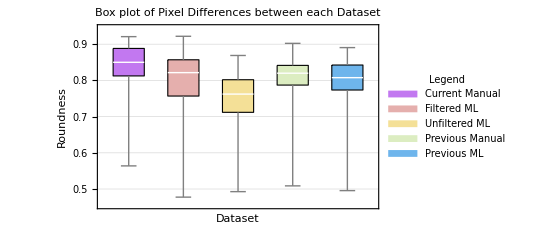

```mathematica
(*Boxplot of roundness*)

(*once image finalised/ use area of that particular image*)
BoxWhiskerChart[{manualASround[[12]],filteredround[[12]],unfilteredround[[12]],manualKSround[[12]],mlKSround[[12]]},ChartStyle->{EdgeForm[Black],"Pastel"},ChartLegends->Placed[SwatchLegend[{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML"},LegendMarkerSize->20,LegendLabel->Style["Legend",Black,Bold,12],LabelStyle->{Black,Bold,12}],Right],FrameLabel->{Style["Dataset",Black,Bold,12],Style["Roundness",Black,Bold,12]},Background->White,LabelStyle->Medium, PlotTheme->"Detailed", PlotLabel->Style["Box plot of Pixel Differences between each Dataset", Black, Bold]]
```

```mathematica
|
```

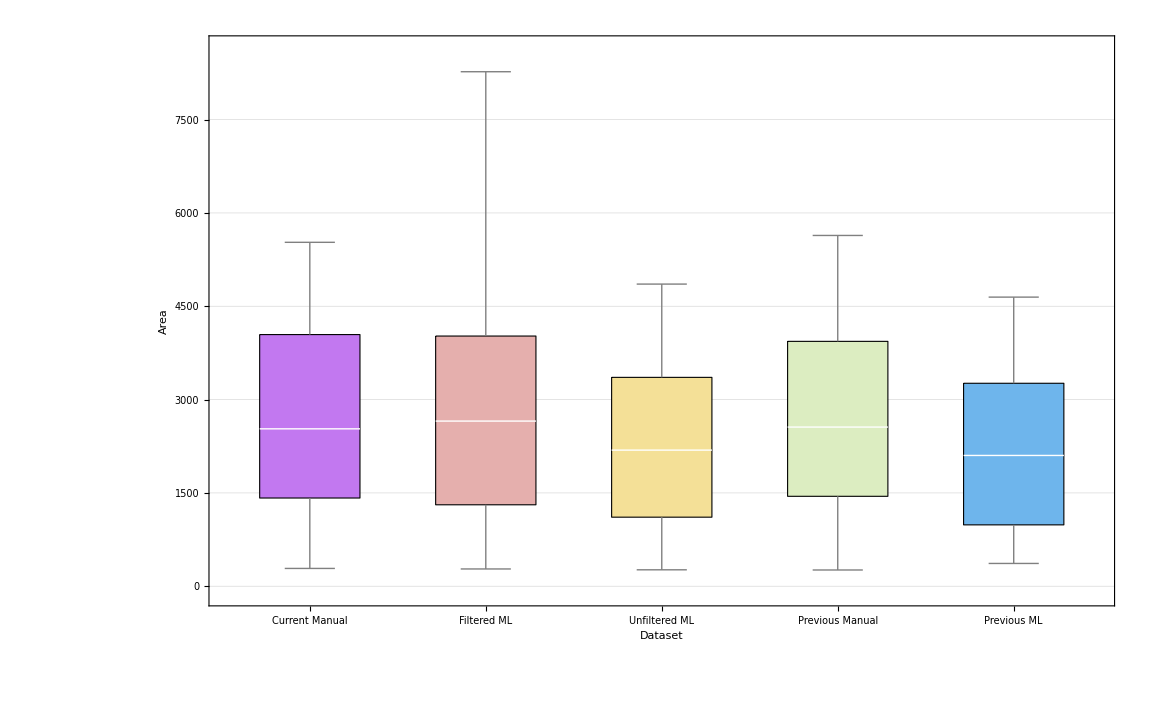

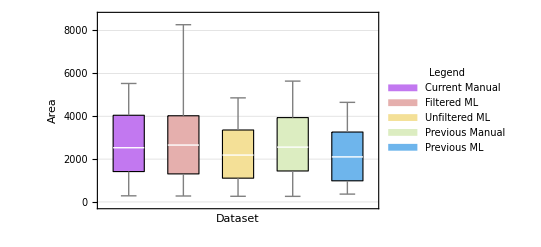

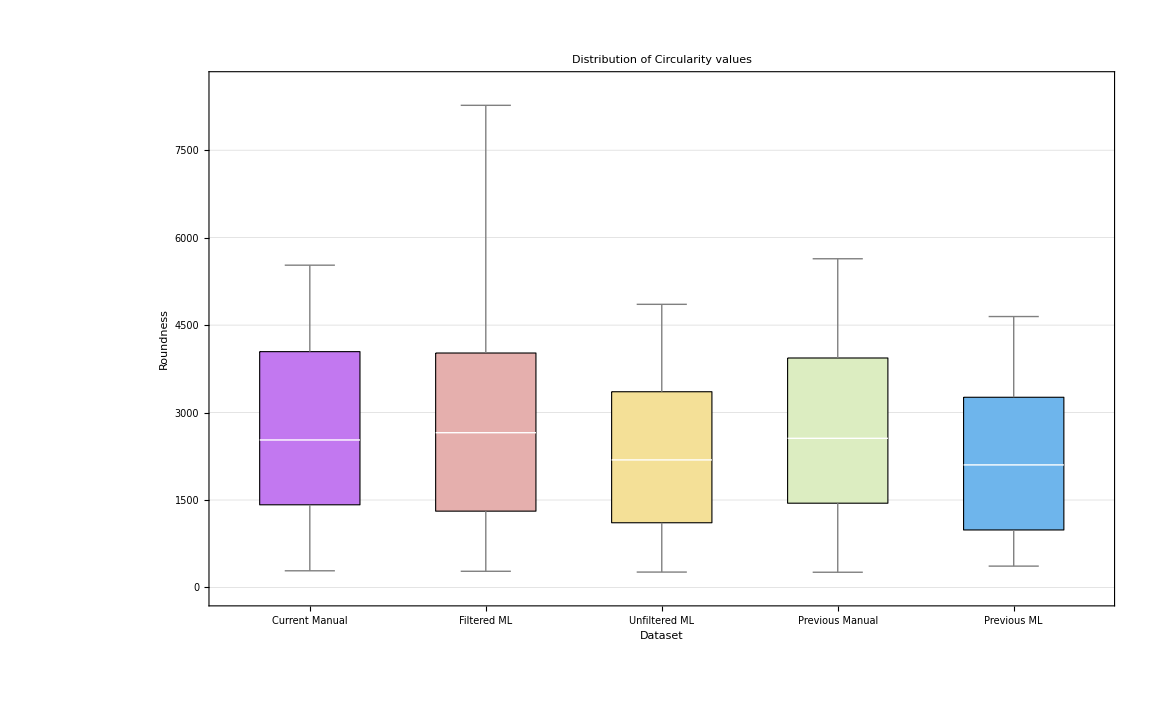

```mathematica
(*Boxplot of area*)
BoxWhiskerChart[{manualASarea[[12]],filteredarea[[12]],unfilteredarea[[12]],manualKSarea[[12]],mlKSarea[[12]]},ChartStyle->{EdgeForm[Black],"Pastel"}, ChartLabels->{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML",Style[Black, Bold]}, Background->White,  PlotTheme->"Detailed", FrameLabel->{Style["Dataset",Black,Bold,18],Style["Area",Black,Bold,18]}, LabelStyle->Directive[Bold, Black,18]]




BoxWhiskerChart[{manualASarea[[12]],filteredarea[[12]],unfilteredarea[[12]],manualKSarea[[12]],mlKSarea[[12]]},ChartStyle->{EdgeForm[Black],"Pastel"},ChartLegends->Placed[SwatchLegend[{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML"},LegendMarkerSize->20,LegendLabel->Style["Legend",Black,Bold,18],LabelStyle->{Black,Bold,18}],Right],FrameLabel->{Style["Dataset",Black,Bold,18],Style["Area",Black,Bold,18]},Background->White,LabelStyle->Medium, PlotTheme->"Detailed"]

(*once image finalised/ use area of that particular image*)


BoxWhiskerChart[{manualASarea[[12]],filteredarea[[12]],unfilteredarea[[12]],manualKSarea[[12]],mlKSarea[[12]]},ChartStyle->{EdgeForm[Black],"Pastel"},  Background->White,  PlotTheme->"Detailed", ChartLabels->{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML",Style[Black, Bold]},FrameLabel->{Style["Dataset",Black,Bold,18],Style["Area (µm.b2)",Black,Bold,18]}, LabelStyle->Directive[Bold, Black,18], PlotLabel->Style["Distribution of Area values", Black, 20]]
```

```mathematica
descriptiveStats={{Mean[#],Median[#],StandardDeviation[#],Min[#],Max[#]}&/@{manualASarea[[12]],filteredarea[[12]],unfilteredarea[[12]],manualKSarea[[12]],mlKSarea[[12]]}}
```

{{{2651.02,2529.94,1448.11,286.125,5527.75},{2792.14,2654.5,1710.69,277.75,8269.63},{2244.6,2187.88,1263.3,264.125,4856.38},{2644.41,2558.19,1481.89,261.125,5638.},{2117.93,2102.13,1204.62,366.25,4646.88}}}

```mathematica
a
filteredarea[[12]]
Correlation[filteredarea[[12]],unfilteredarea[[12]]]
```

{0.818044,0.840484,0.892386,0.88281,0.901154,0.87729,0.925385,0.902244,0.8784,0.870712,0.851254,0.86445,0.860974,0.846694,0.837237,0.854486,0.862355,0.855023,0.828603,0.792545,0.856667,0.738658,0.771962,0.790534,0.755528,0.743845}

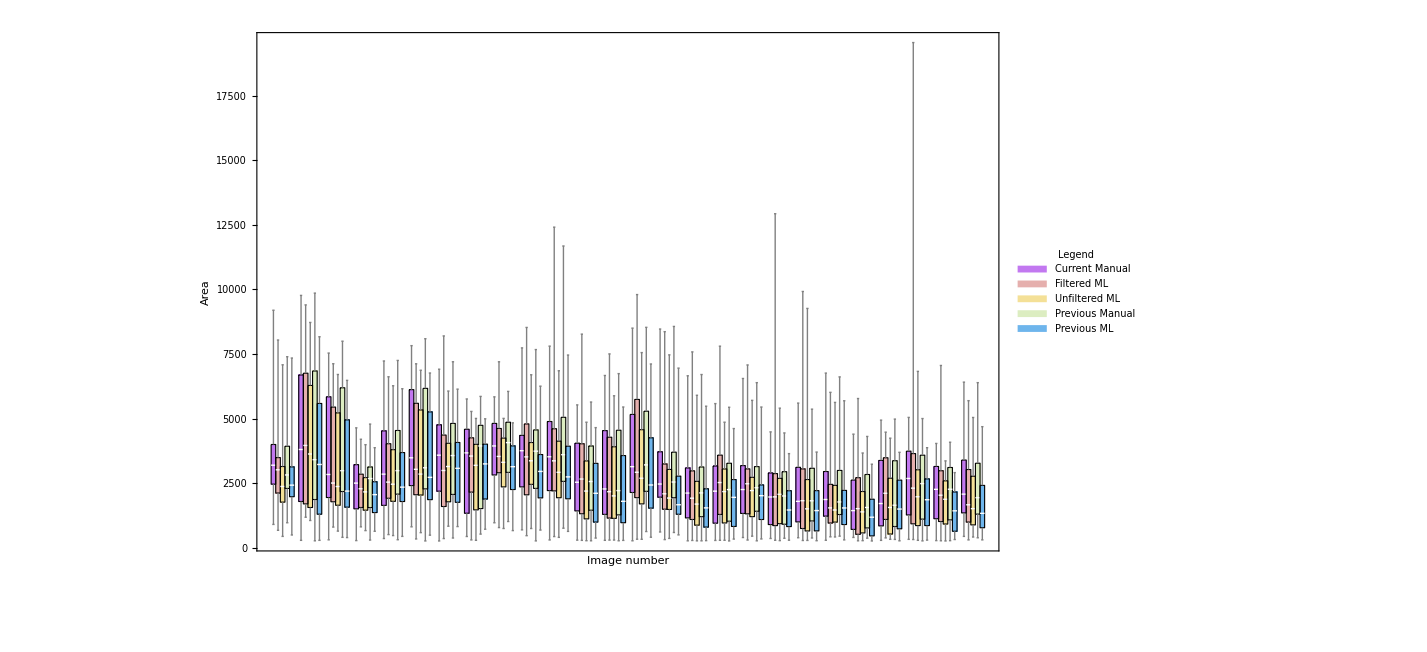

```mathematica
(*grouped by image number, area*)

(*Concatenate the datasets into a single list*)
allData={manualASarea,filteredarea,unfilteredarea,manualKSarea,mlKSarea};

(*Transpose the data to group them by image number*)
transposedData=Transpose[allData];
numImages=Length[manualASarea];
grpLabels=Range[numImages];
(*Create a BoxWhiskerChart with space between groups*)
BoxWhiskerChart[transposedData,ChartStyle->{EdgeForm[Black],"Pastel"},Background->White,LabelStyle->Medium,ChartLayout->"Grouped",(*Use "Grouped" layout*)BarSpacing->{0,1}, ChartLegends->Placed[SwatchLegend[{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML"},LegendMarkerSize->20,LegendLabel->Style["Legend",Black,Bold,12],LabelStyle->{Black,Bold,12}],Right],FrameLabel->{Style["Image number",Black,Bold,12],Style["Area",Black,Bold,12]},Background->White,LabelStyle->Medium(*Adjust the spacing between groups*)
]
```

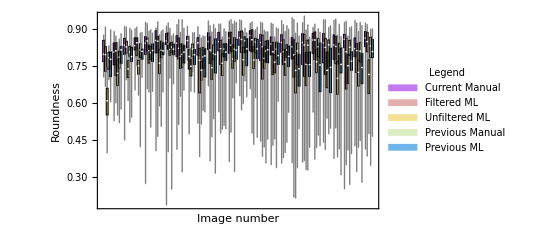

```mathematica
(*grouped by image no, circularity*)
(*Concatenate the datasets into a single list*)
allData={manualASround,filteredround,unfilteredround,manualKSround,mlKSround};

(*Transpose the data to group them by image number*)
transposedData=Transpose[allData];
numImages=Length[manualASround];
grpLabels=Range[numImages];
(*Create a BoxWhiskerChart with space between groups*)
BoxWhiskerChart[transposedData,ChartStyle->{EdgeForm[Black],"Pastel"},Background->White,LabelStyle->Medium,ChartLayout->"Grouped",(*Use "Grouped" layout*)BarSpacing->{0,1}, ChartLegends->Placed[SwatchLegend[{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML"},LegendMarkerSize->20,LegendLabel->Style["Legend",Black,Bold,12],LabelStyle->{Black,Bold,12}],Right],FrameLabel->{Style["Image number",Black,Bold,12],Style["Roundness",Black,Bold,12]},Background->White,LabelStyle->Medium(*Adjust the spacing between groups*)]
```

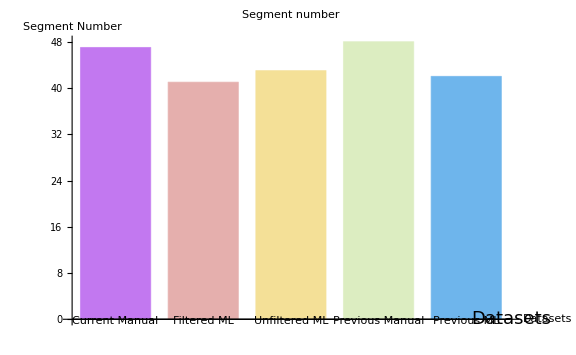

```mathematica
(*segment no graphs*)
(*extract segment numbers:*)
filteredseg=filtered[[All,All, 1]];
unfilteredseg=unfiltered[[All,All,1]];
manualASseg=manualAS[[All,All,1]];
manualKSseg=manualKS[[All,All,1]];
mlKSseg=mlKS[[All,All,1]];

filteredseg=DeleteCases[filteredseg,_String,{2}];
unfilteredseg=DeleteCases[unfilteredseg,_String,{2}];
manualASseg=DeleteCases[manualASseg,_String,{2}];
manualKSseg=DeleteCases[manualKSseg,_String,{2}];
mlKSseg=DeleteCases[mlKSseg,_String,{2}];

(*graph diff in segment nos for singke image*)
BarChart[{Length[manualASseg[[13]]],Length[filteredseg[[13]]],Length[unfilteredseg[[13]]],Length[manualKSseg[[13]]],Length[mlKSseg[[13]]]},ChartLabels->{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML"},PlotLabel->"Segment number",AxesLabel->{Style["Datasets",Black,18],Style["Segment Number",Black,Bold,18]},ImageSize->Large,BarSpacing->Medium,ChartStyle->"Pastel", Background->White, LabelStyle->Directive[Bold, Black,18], ChartStyle->{EdgeForm[Black],"Pastel"}]
```

{{18,23,26,14,31,28,38,45,39,41,29,56,47,40,33,52,68,57,47,59,22,44,60,63,53,34},{17,19,25,13,29,28,35,40,33,32,26,45,41,35,31,43,46,41,38,46,19,36,50,40,42,31},{18,20,25,13,29,28,36,44,38,36,28,56,43,39,34,52,59,50,41,56,20,38,57,60,51,35},{16,22,26,14,30,30,37,46,40,43,27,58,48,39,33,52,65,58,47,65,24,49,60,64,53,35},{18,21,26,13,29,28,36,43,40,39,29,55,42,38,33,50,63,56,46,57,25,50,50,57,57,34}}

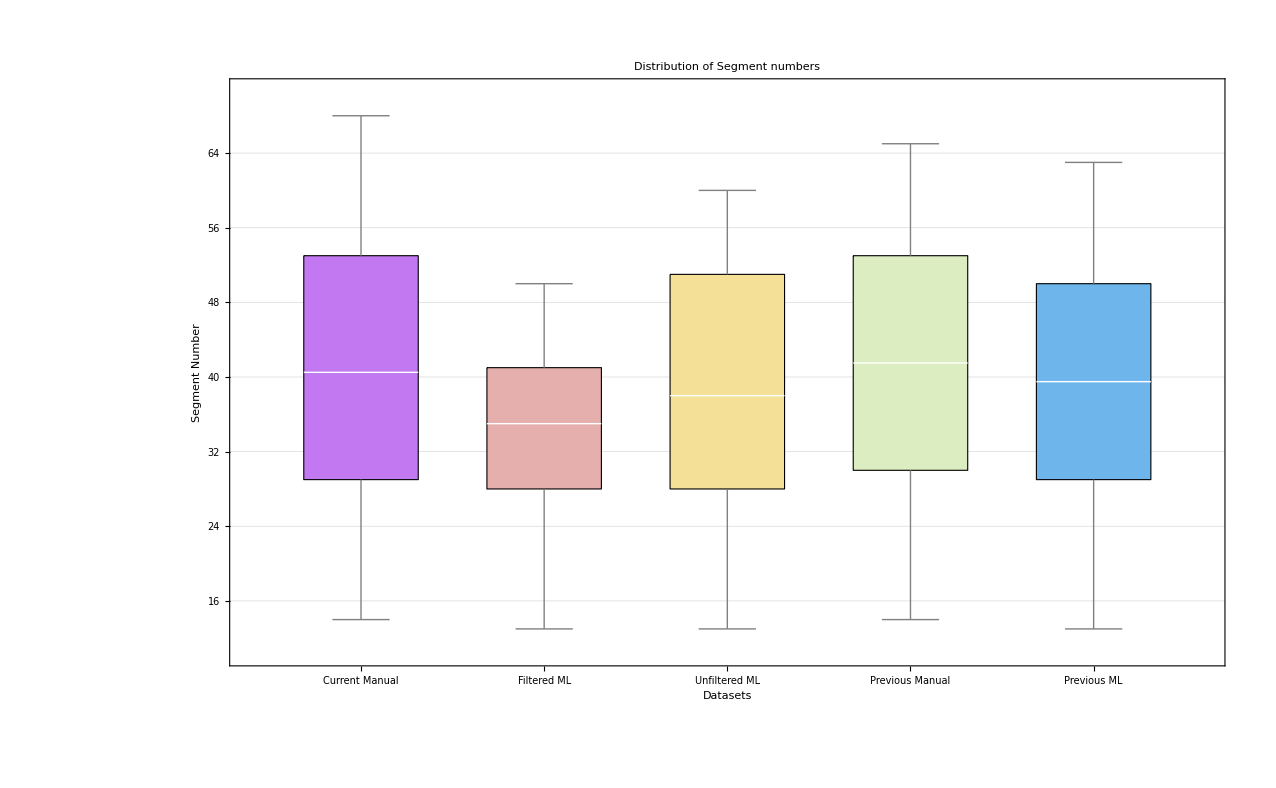

```mathematica
x={Last/@manualASseg,Last/@filteredseg, Last/@unfilteredseg, Last/@manualKSseg, Last/@mlKSseg}

BoxWhiskerChart[{x},ChartLabels->{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML"},AxesLabel->{Style["Datasets",Black,22],Style["Segment Number",Black,Bold,22]},ImageSize->Large,BarSpacing->Medium, Background->White, LabelStyle->Directive[Bold, Black,22], PlotTheme->"Detailed", ChartStyle->{EdgeForm[Black],"Pastel"}, PlotLabel->"Distribution of Segment numbers"]
```

{1067/26,881/26,503/13,1081/26,1035/26}

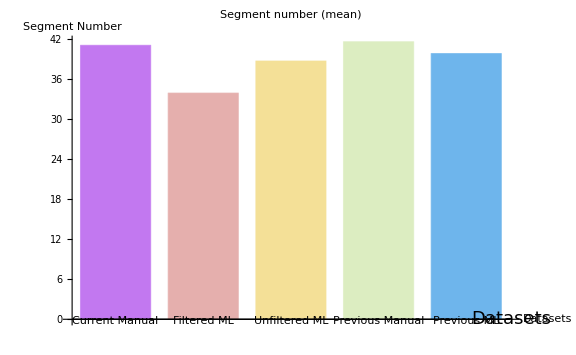

```mathematica
x={Mean[Last/@manualASseg],Mean[Last/@filteredseg],Mean[ Last/@unfilteredseg], Mean[Last/@manualKSseg], Mean[Last/@mlKSseg]}

BarChart[{x},ChartLabels->{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML"},PlotLabel->"Segment number (mean)",AxesLabel->{Style["Datasets",Black,18],Style["Segment Number",Black,Bold,18]},ImageSize->Large,BarSpacing->Medium,ChartStyle->"Pastel", Background->White, LabelStyle->Directive[Bold, Black,18]]
```

```mathematica
Needs["ANOVA`"]
(*anova of segment nos*)
(*data={Last/@manualASseg,Last/@filteredseg, Last/@unfilteredseg, Last/@manualKSseg, Last/@mlKSseg}*)

labeledlist=Flatten[MapIndexed[{First@#2,#1}&,{ Last/@manualASseg,Last/@filteredseg, Last/@unfilteredseg, Last/@manualKSseg, Last/@mlKSseg},{2}],1];
ANOVA[labeledlist]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 4 | 980.462 | 245.115 | 1.32802 | 0.263202
Error | 125 | 23071.5 | 184.572 |  | 
Total | 129 | 24052. |  |  | ,CellMeans→All | 39.
Model[1] | 41.0385
Model[2] | 33.8846
Model[3] | 38.6923
Model[4] | 41.5769
Model[5] | 39.8077}

```mathematica
Last/@manualASseg
```

{18,23,26,14,31,28,38,45,39,41,29,56,47,40,33,52,68,57,47,59,22,44,60,63,53,34}

```mathematica
(*means of area and roundness*)

meanfiltar=Mean/@filteredarea;
meanunfiltar=Mean/@unfilteredarea;
meanmanASar=Mean/@manualASarea;
meanmanKSar=Mean/@manualKSarea;
meanmlKSar=Mean/@mlKSarea;
meanfunfilar=Mean/@funfiltarea;

meanfiltro=Mean/@filteredround;
meanunfilro=Mean/@unfilteredround;
meanmanASro=Mean/@manualASround;
meanmanKSro=Mean/@manualKSround;
meanmlKSro=Mean/@mlKSround;
meanfunfilro=Mean/@funfiltround;
```

{ Current Manual,Filtered ML,Unfiltered ML,Previous Manual,Previous ML}

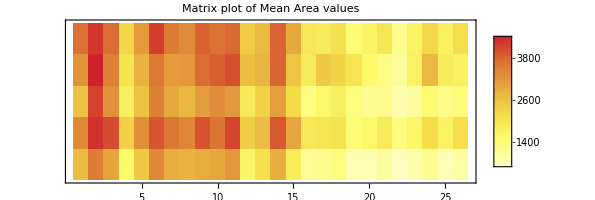

{ Current Manual,Filtered ML,Unfiltered ML,Previous Manual,Previous ML}

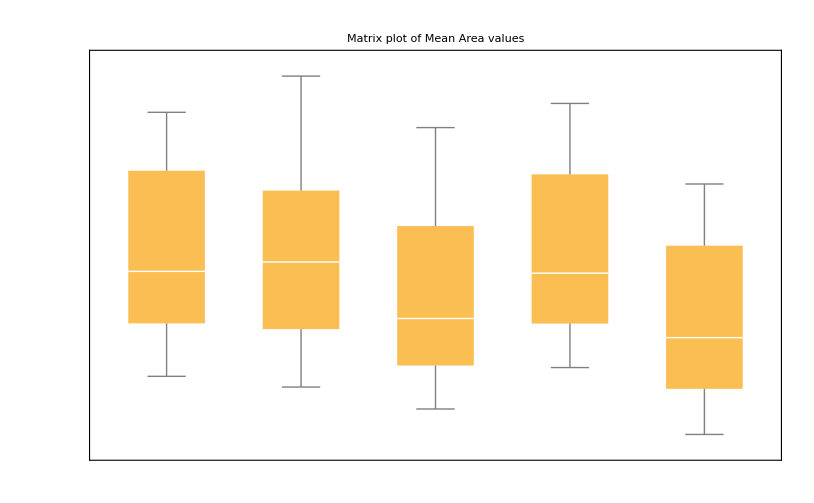

{3011.75,1657.25,1602.,2277.88,1691.25,593.125,3074.5,4254.75,2938.25,1831.25,6689.38,2861.,1000.75,2916.75,4800.63,1861.75,3526.,2215.75,1072.38,1921.13}

```mathematica
(*area matrix plot*)

datasets={" Current Manual", "Filtered ML", "Unfiltered ML", "Previous Manual", "Previous ML"}
MatrixPlot[{meanmanASar,meanfiltar,meanunfiltar,meanmanKSar,meanmlKSar},ColorFunction->"TemperatureMap", PlotLegends->Automatic, PlotLabel->Style["Matrix plot of Mean Area values", Black, 20],Background->White, LabelStyle->Directive[Bold, Medium, Black, 18], FrameTicks->{{None,Transpose[{Range[5],datasets}]}, {Automatic, Automatic}}
]

(*add titles*)

datasets={" Current Manual", "Filtered ML", "Unfiltered ML", "Previous Manual", "Previous ML"}
BoxWhiskerChart[{meanmanASar,meanfiltar,meanunfiltar,meanmanKSar,meanmlKSar}, PlotLabel->Style["Matrix plot of Mean Area values", Black, 20],Background->White, LabelStyle->Directive[Bold, Medium, Black, 18], FrameTicks->{{None,Transpose[{Range[5],datasets}]}, {Automatic, Automatic}}
]
```

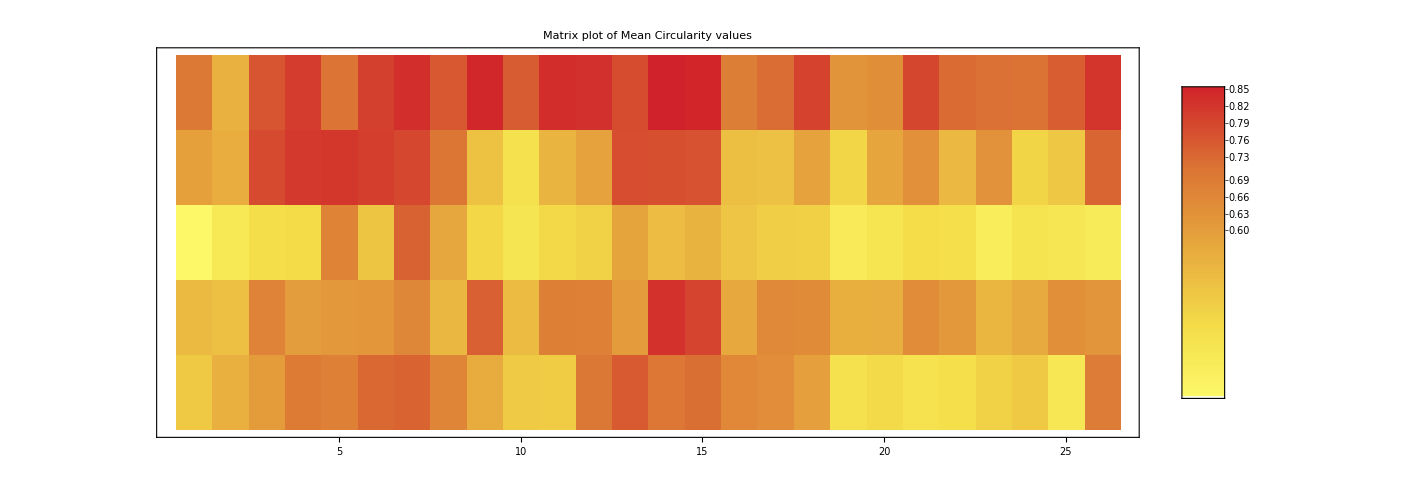

```mathematica
(*roundness matrix plot*)
MatrixPlot[{meanmanASro,meanfiltro,meanunfilro,meanmanKSro,meanmlKSro},ColorFunction->"TemperatureMap", PlotLegends->Automatic,Background->White, PlotLabel->Style["Matrix plot of Mean Circularity values", Black, 20],LabelStyle->Directive[Bold, Medium, Black, 18],  FrameTicks->{{None,Transpose[{Range[5],datasets}]}, {Automatic, Automatic}}]
```

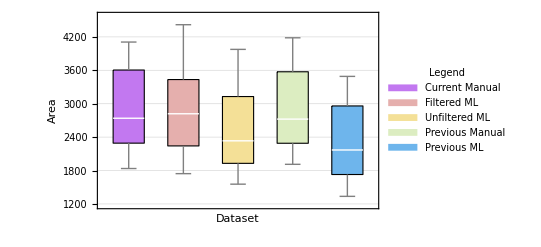

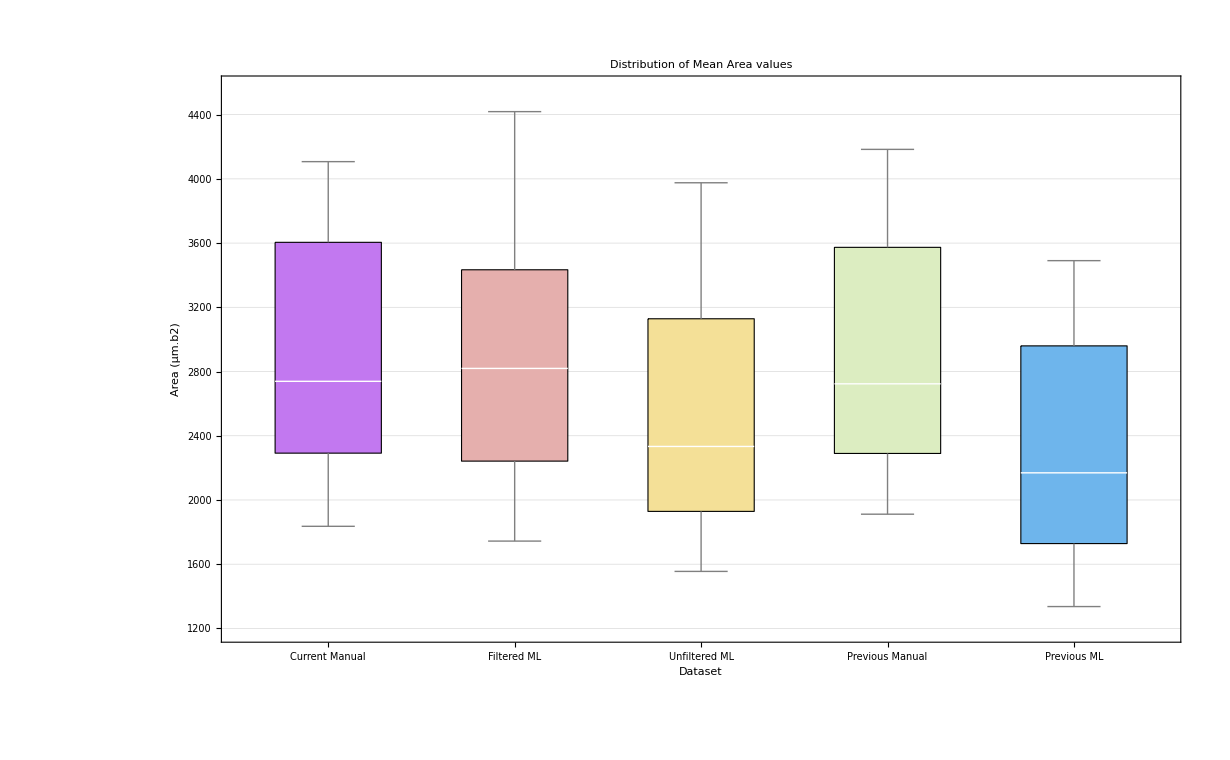

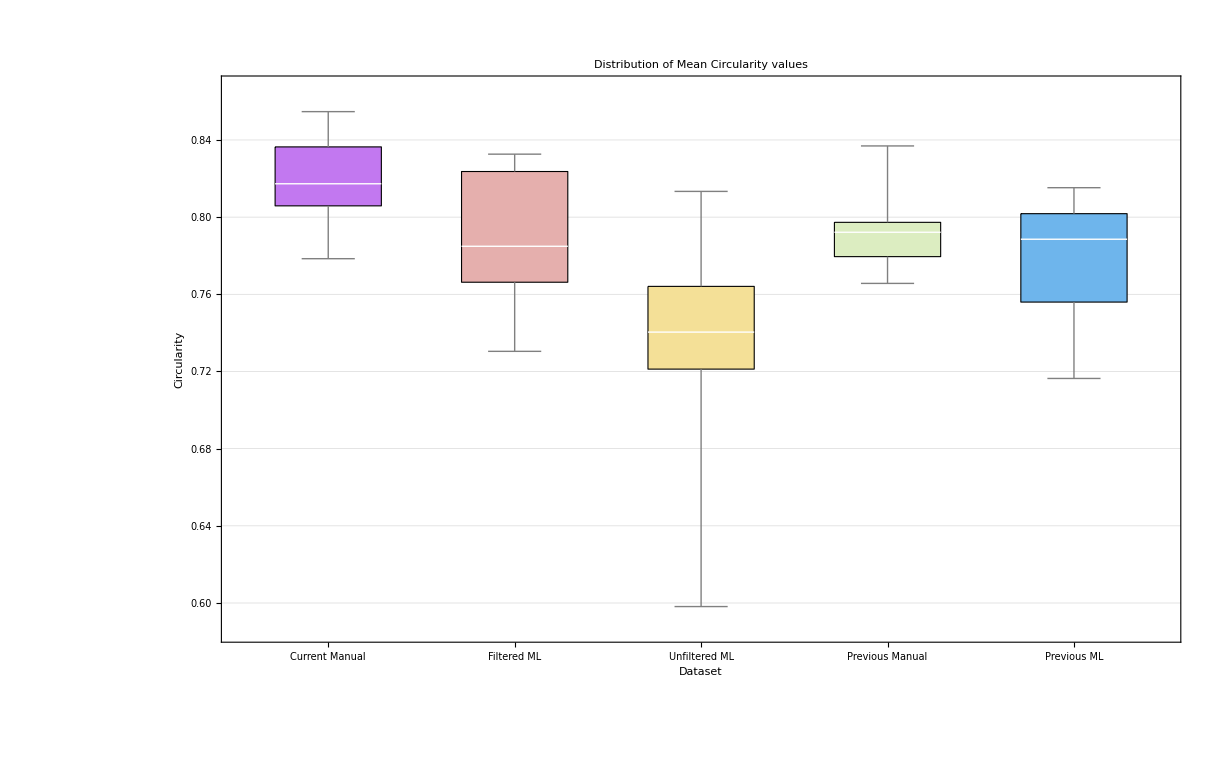

{0.0250484,0.0401532,0.00727056,0.586411,0.159911,0.039699,0.274584,0.00321465,0.727385,0.129872,0.00839186,0.0167927,0.0076774,0.0120098,0.000423402,0.000921998,0.0164935,0.0224516,2.43173×10^-7,1.44492×10^-6,0.0052319,0.0034269,0.00265956,6.25521×10^-9,0.00702129,0.00210313}

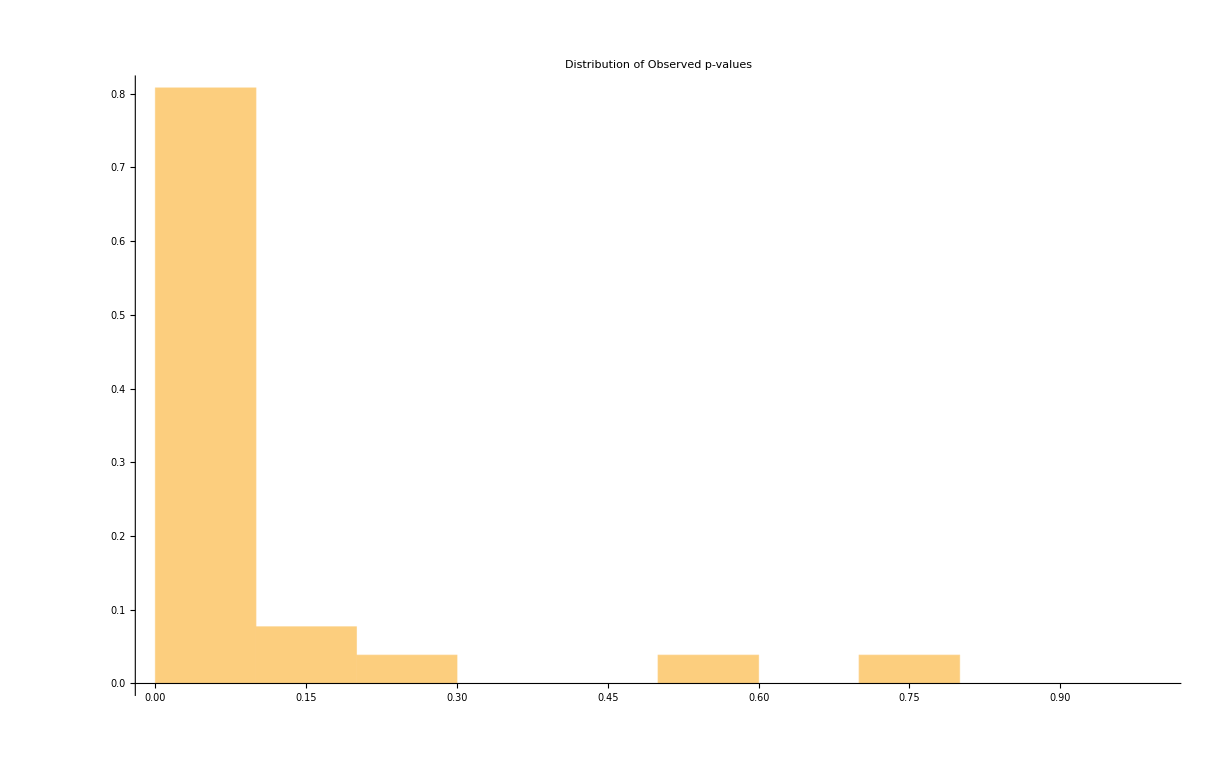

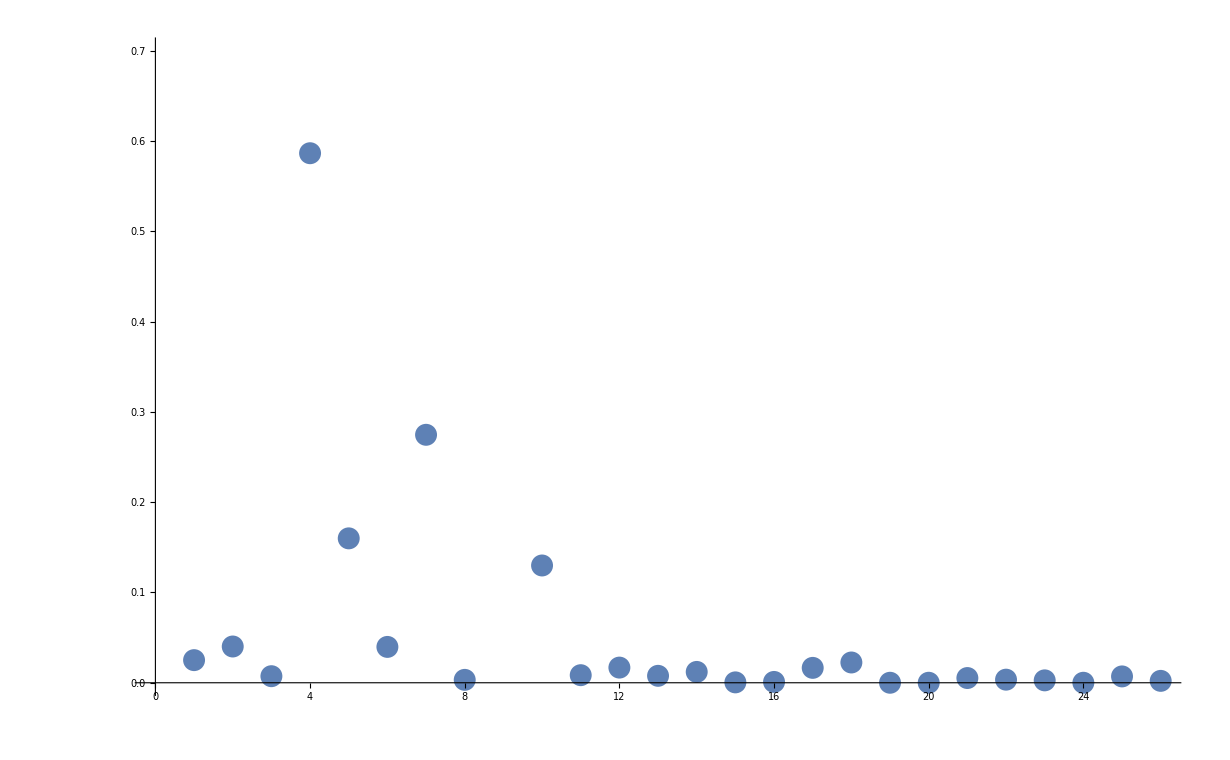

```mathematica
BoxWhiskerChart[{meanmanASar,meanfiltar,meanunfiltar,meanmanKSar,meanmlKSar},ChartStyle->{EdgeForm[Black],"Pastel"},ChartLegends->Placed[SwatchLegend[{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML"},LegendMarkerSize->20,LegendLabel->Style["Legend",Black,Bold,18],LabelStyle->{Black,Bold,18}],Right],FrameLabel->{Style["Dataset",Black,Bold,18],Style["Area",Black,Bold,18]},Background->White,LabelStyle->Medium, PlotTheme->"Detailed"]

(*once image finalised/ use area of that particular image*)


BoxWhiskerChart[{meanmanASar,meanfiltar,meanunfiltar,meanmanKSar,meanmlKSar},ChartStyle->{EdgeForm[Black],"Pastel"},  Background->White,  PlotTheme->"Detailed", ChartLabels->{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML",Style[Black, Bold]},FrameLabel->{Style["Dataset",Black,Bold,22],Style["Area (µm.b2)",Black,Bold,22]}, LabelStyle->Directive[Bold, Black,22], PlotLabel->Style["Distribution of Mean Area values", Black, 22]]


BoxWhiskerChart[{meanmanASro,meanfiltro,meanunfilro,meanmanKSro,meanmlKSro},ChartStyle->{EdgeForm[Black],"Pastel"},  Background->White,  PlotTheme->"Detailed", ChartLabels->{"Current Manual","Filtered ML","Unfiltered ML","Previous Manual","Previous ML",Style[Black, Bold]},FrameLabel->{Style["Dataset",Black,Bold,22],Style["Circularity",Black,Bold,22]}, LabelStyle->Directive[Bold, Black,22], PlotLabel->Style["Distribution of Mean Circularity values", Black, 22]]






(*calc area p-values*)
pValues1=Map[ShapiroWilkTest,filteredarea]
Histogram[pValues1,Automatic,"Probability",PlotRange->{{0,1},Automatic},FrameLabel->{"p-value","Probability"},PlotLabel->"Distribution of Observed p-values"]
ListPlot[pValues1, PlotRange-> {0,0.7}]
```

{0.0229218,0.0531898,0.00743552,0.611871,0.137751,0.0175843,0.424795,0.00415909,0.045661,0.420811,0.327261,0.0198969,0.00536102,0.0328517,0.00156679,0.000661586,0.0260688,0.0357993,0.0450325,9.30484×10^-8,0.00943828,0.00216738,0.000291139,0.000654095,0.00915353,0.000704061}

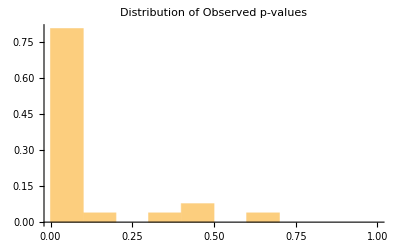

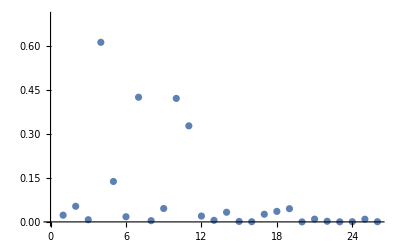

{0.0250484,0.0401532,0.00727056,0.586411,0.159911,0.039699,0.274584,0.00321465,0.727385,0.129872,0.00839186,0.0167927,0.0076774,0.0120098,0.000423402,0.000921998,0.0164935,0.0224516,2.43173×10^-7,1.44492×10^-6}

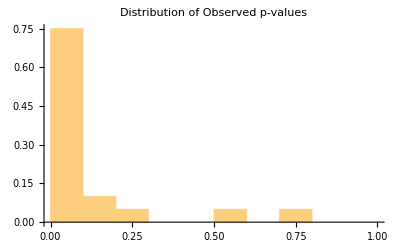

```mathematica
pValues2=Map[ShapiroWilkTest,unfilteredarea]
Histogram[pValues2,Automatic,"Probability",PlotRange->{{0,1},Automatic},FrameLabel->{"p-value","Probability"},PlotLabel->"Distribution of Observed p-values"]
ListPlot[pValues2, PlotRange-> {0,0.7}]
```

{0.0157414,0.0778469,0.022522,0.949522,0.270712,0.0260313,0.867228,0.00115531,0.113493,0.544178,0.532452,0.0297811,0.00610172,0.0342091,0.00354244,0.00607325,0.00778218,0.0214753,0.0621101,0.00371325,0.020269,0.00033485,0.000385947,0.0156492,0.0176251,0.00477205}

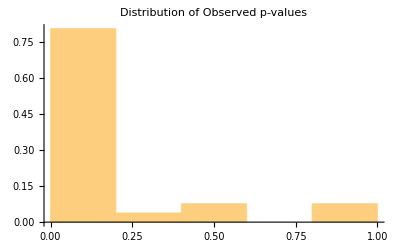

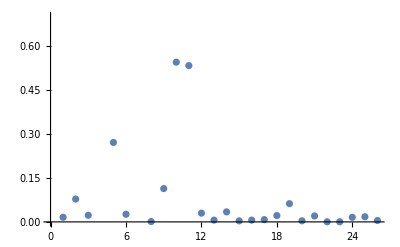

```mathematica
pValues3=Map[ShapiroWilkTest,manualASarea]
Histogram[pValues3,Automatic,"Probability",PlotRange->{{0,1},Automatic},FrameLabel->{"p-value","Probability"},PlotLabel->"Distribution of Observed p-values"]
ListPlot[pValues3, PlotRange-> {0,0.7}]
```

{0.0423984,0.0732368,0.0247001,0.946592,0.334642,0.0528159,0.786738,0.000655203,0.0875215,0.595051,0.0202466,0.0450607,0.00500187,0.0212213,0.00380977,0.0105401,0.0235376,0.0392871,0.0353116,0.00342208,0.0128074,0.000437426,0.000183807,0.0079491,0.0242034,0.0034804}

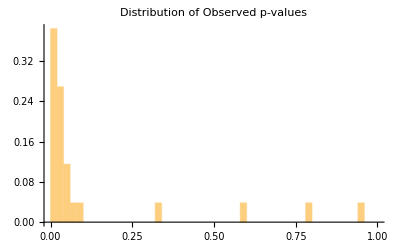

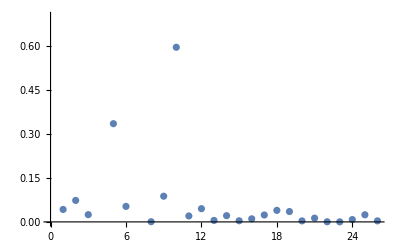

```mathematica
pValues4=Map[ShapiroWilkTest,manualKSarea]
Histogram[pValues4,Automatic,"Probability",PlotRange->{{0,1},Automatic},FrameLabel->{"p-value","Probability"},PlotLabel->"Distribution of Observed p-values"]
ListPlot[pValues4, PlotRange-> {0,0.7}]
```

{0.013472,0.070517,0.00967951,0.604432,0.135736,0.0152269,0.348872,0.00243052,0.0784574,0.301177,0.120043,0.0112409,0.00421268,0.0148286,0.00109373,0.00102641,0.00662497,0.00968463,0.0380376,0.00693992,0.00551252,0.000321143,0.00297489,0.0119573,0.00124266,0.000681914}

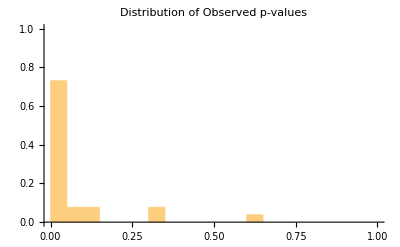

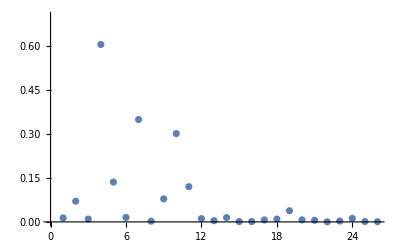

```mathematica
pValues5=Map[ShapiroWilkTest,mlKSarea]
Histogram[pValues5,Automatic,"Probability",PlotRange->{{0,1},{0,1}},FrameLabel->{"p-value","Probability"},PlotLabel->"Distribution of Observed p-values"]
ListPlot[pValues5, PlotRange-> {0,0.7}]
```

{0.774719,0.0112687,0.177572,0.561482,0.0103651,0.0000247671,3.43152×10^-7,0.000413384,0.000270935,0.00325022,0.000390823,0.0000944483,8.78654×10^-6,8.03948×10^-6,0.0000102676,0.0000211242,0.000417059,0.0000841928,0.000139216,4.84671×10^-6,0.000152087,0.000249676,0.0000160434,0.000792529,0.000137286,4.39621×10^-6}

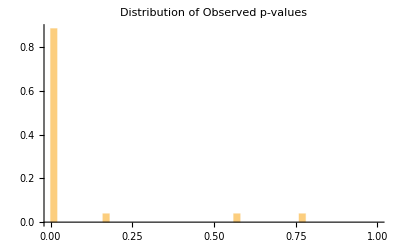

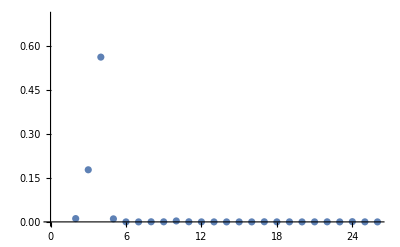

```mathematica
(*round p-values*)

pValues6=Map[ShapiroWilkTest,filteredround]
Histogram[pValues6,26,"Probability",PlotRange->{{0,1},Automatic},FrameLabel->{"p-value","Probability"},PlotLabel->"Distribution of Observed p-values"]
ListPlot[pValues6, PlotRange-> {0,0.7}]
```

{0.968559,0.482937,0.304838,0.0934751,0.576196,0.292148,0.582421,0.0817328,0.407004,0.0636815,0.0916385,0.0096001,0.818792,0.131323,0.000206808,0.0000323652,0.0000118282,0.0000756557,0.000750388,0.0000677621,0.000482003,0.0656611,0.0317529,0.000134824,0.00272224,0.0105761}

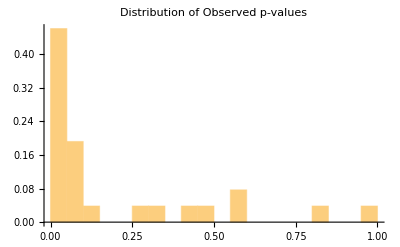

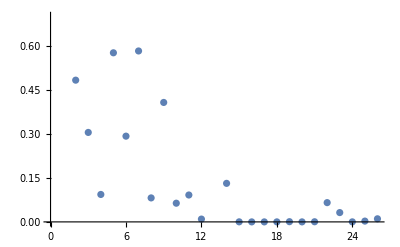

```mathematica
pValues7=Map[ShapiroWilkTest,unfilteredround]
Histogram[pValues7,26,"Probability",PlotRange->{{0,1},Automatic},FrameLabel->{"p-value","Probability"},PlotLabel->"Distribution of Observed p-values"]
ListPlot[pValues7, PlotRange-> {0,0.7}]
```

{0.382321,0.00193446,2.12985×10^-6,0.0132007,2.30117×10^-7,1.50762×10^-6,5.63306×10^-11,2.15356×10^-7,0.391212,0.0000463087,0.0238221,5.63348×10^-6,1.35853×10^-7,0.0000456109,0.000180189,3.19904×10^-7,2.28736×10^-9,2.47736×10^-9,5.25724×10^-7,2.98663×10^-8,0.000250865,0.0000409919,8.96233×10^-8,1.1984×10^-11,3.0035×10^-6,6.7816×10^-8}

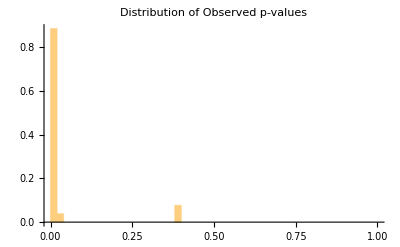

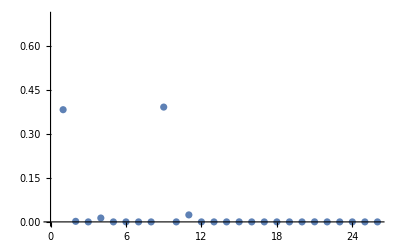

```mathematica
pValues8=Map[ShapiroWilkTest,manualASround]
Histogram[pValues8,26,"Probability",PlotRange->{{0,1},Automatic},FrameLabel->{"p-value","Probability"},PlotLabel->"Distribution of Observed p-values"]
ListPlot[pValues8, PlotRange-> {0,0.7}]
```

{0.0811017,0.00137437,7.42525×10^-6,0.0000279893,0.000663075,0.0000224183,1.46689×10^-10,7.56214×10^-7,0.477868,0.000524755,0.000660094,8.36757×10^-8,1.23396×10^-7,0.015256,0.0000987413,9.8992×10^-8,2.75498×10^-9,2.21464×10^-8,1.52×10^-6,4.04722×10^-9,0.0000459615,8.37554×10^-6,4.14501×10^-7,1.55483×10^-10,7.33701×10^-6,2.56453×10^-7}

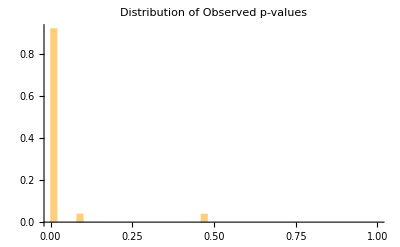

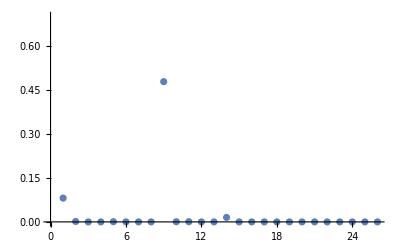

```mathematica
pValues9=Map[ShapiroWilkTest,manualKSround]
Histogram[pValues9,26,"Probability",PlotRange->{{0,1},Automatic},FrameLabel->{"p-value","Probability"},PlotLabel->"Distribution of Observed p-values"]
ListPlot[pValues9, PlotRange-> {0,0.7}]
```

{0.902063,0.00204714,0.00332748,0.591665,0.178445,0.0633311,0.0134113,0.304983,0.0256227,0.0174129,0.0000197491,2.37753×10^-6,0.18243,0.00146501,0.0000216796,1.1938×10^-6,0.233637,0.0285369,0.436787,8.96316×10^-6,0.0199722,0.109226,8.47516×10^-6,0.000132548,0.0000562835,0.0000599827}

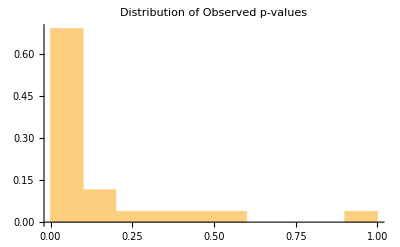

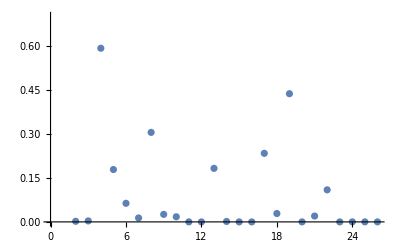

```mathematica
pValues10=Map[ShapiroWilkTest,mlKSround]
Histogram[pValues10,Automatic,"Probability",PlotRange->{{0,1},Automatic},FrameLabel->{"p-value","Probability"},PlotLabel->"Distribution of Observed p-values"]
ListPlot[pValues10, PlotRange-> {0,0.7}]
```

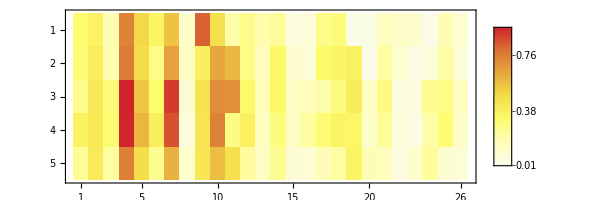

```mathematica
(*area p-values matrix*)
MatrixPlot[{pValues1,pValues2,pValues3,pValues4,pValues5},ColorFunction->"TemperatureMap", PlotLegends->Automatic]
```

```mathematica
?
```

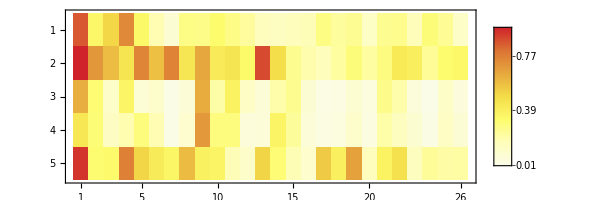

```mathematica
(*roundness p-values matrix*)
MatrixPlot[{pValues6,pValues7,pValues8,pValues9,pValues10},ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

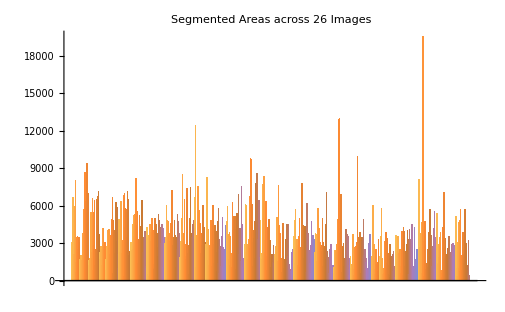

```mathematica
BarChart[filteredarea,PlotLabel->"Segmented Areas across 26 Images",FrameLabel->{"Image Index","Segmented Area"}]
```

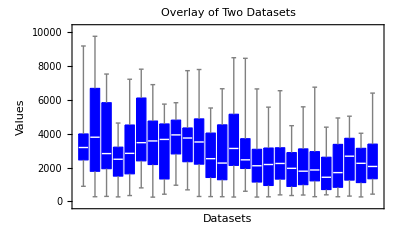

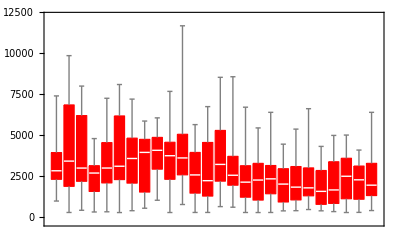

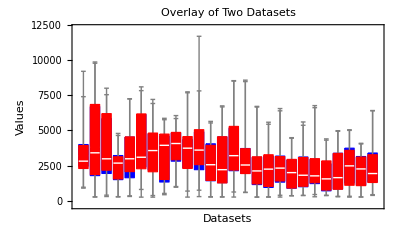

```mathematica
chart1=BoxWhiskerChart[manualASarea,ChartStyle->Directive[Blue,EdgeForm[{Thick,Blue}]],PlotLabel->"Overlay of Two Datasets",FrameLabel->{"Datasets","Values"},ChartStyle->"Pastel"]

(*Create a box whisker chart for the second dataset*)
chart2=BoxWhiskerChart[manualKSarea,ChartStyle->Directive[Red,EdgeForm[{Thick,Red}]]]

(*Overlay the two charts*)
Show[chart1,chart2]
```

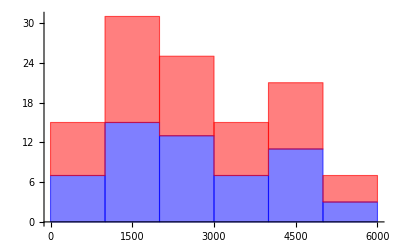

```mathematica
Histogram[{manualASarea[[12]],manualKSarea[[12]]},ChartStyle->{Blue,Red,Green},ChartLayout->"Stacked",ChartStyle->{EdgeForm[Black],"Pastel"}]
```

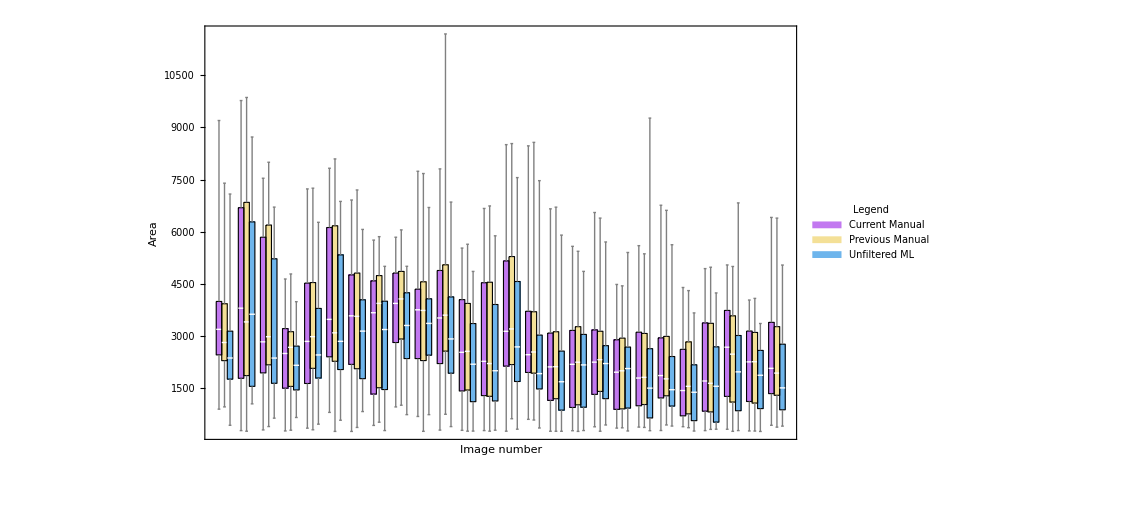

```mathematica
(*comparing area for manual AS, Manual KS and ML unifltered*)
(*Concatenate the datasets into a single list*)
combinedData={manualASarea,manualKSarea,unfilteredarea};

(*Transpose the data to group them by image number*)
transposedData=Transpose[combinedData];
numImages=Length[manualASarea];
grpLabels=Range[numImages];
(*Create a BoxWhiskerChart with space between groups*)
BoxWhiskerChart[transposedData,ChartStyle->{EdgeForm[Black],"Pastel"},Background->White,LabelStyle->Medium,ChartLayout->"Grouped",(*Use "Grouped" layout*)BarSpacing->{0,1}, ChartLegends->Placed[SwatchLegend[{"Current Manual","Previous Manual","Unfiltered ML"},LegendMarkerSize->20,LegendLabel->Style["Legend",Black,Bold,12],LabelStyle->{Black,Bold,12}],Right],FrameLabel->{Style["Image number",Black,Bold,12],Style["Area",Black,Bold,12]},Background->White,LabelStyle->Medium(*Adjust the spacing between groups*)]
```

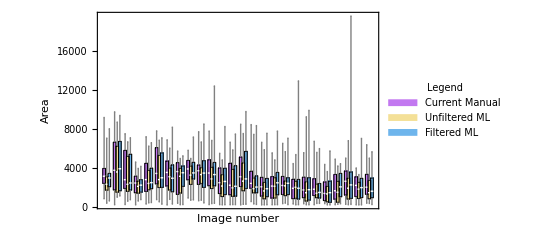

```mathematica
(*comparing area for manual AS, ML filtered,ML unifltered*)
(*Concatenate the datasets into a single list*)
combinedData={manualASarea,unfilteredarea, filteredarea};

(*Transpose the data to group them by image number*)
transposedData=Transpose[combinedData];
numImages=Length[manualASarea];
grpLabels=Range[numImages];
(*Create a BoxWhiskerChart with space between groups*)
BoxWhiskerChart[transposedData,ChartStyle->{EdgeForm[Black],"Pastel"},Background->White,LabelStyle->Medium,ChartLayout->"Grouped",(*Use "Grouped" layout*)BarSpacing->{0,1}, ChartLegends->Placed[SwatchLegend[{"Current Manual","Unfiltered ML", "Filtered ML"},LegendMarkerSize->20,LegendLabel->Style["Legend",Black,Bold,12],LabelStyle->{Black,Bold,12}],Right],FrameLabel->{Style["Image number",Black,Bold,12],Style["Area",Black,Bold,12]},Background->White,LabelStyle->Medium(*Adjust the spacing between groups*)]
```

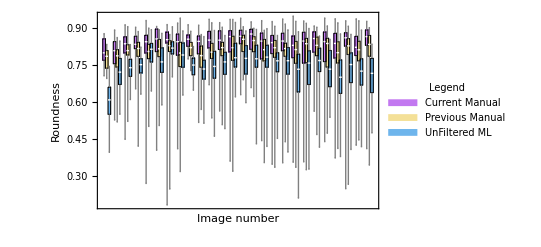

```mathematica
(*comparing area for manual AS, Manual KS and ML unifltered*)
(*Concatenate the datasets into a single list*)
combinedData={manualASround,manualKSround,unfilteredround};

(*Transpose the data to group them by image number*)
transposedData=Transpose[combinedData];
numImages=Length[manualASround];
grpLabels=Range[numImages];
(*Create a BoxWhiskerChart with space between groups*)
BoxWhiskerChart[transposedData,ChartStyle->{EdgeForm[Black],"Pastel"},Background->White,LabelStyle->Medium,ChartLayout->"Grouped",(*Use "Grouped" layout*)BarSpacing->{0,1}, ChartLegends->Placed[SwatchLegend[{"Current Manual","Previous Manual","UnFiltered ML"},LegendMarkerSize->20,LegendLabel->Style["Legend",Black,Bold,12],LabelStyle->{Black,Bold,12}],Right],FrameLabel->{Style["Image number",Black,Bold,12],Style["Roundness",Black,Bold,12]},Background->White,LabelStyle->Medium(*Adjust the spacing between groups*)]
```

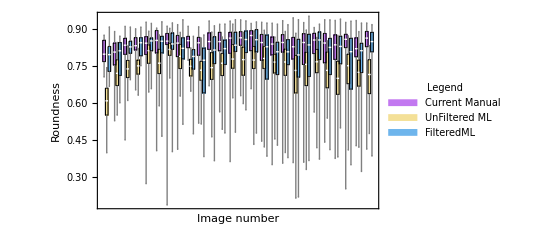

```mathematica
(*comparing area for manual AS, ML filtered and ML unifltered*)
(*Concatenate the datasets into a single list*)
combinedData={manualASround,unfilteredround, filteredround};

(*Transpose the data to group them by image number*)
transposedData=Transpose[combinedData];
numImages=Length[manualASround];
grpLabels=Range[numImages];
(*Create a BoxWhiskerChart with space between groups*)
BoxWhiskerChart[transposedData,ChartStyle->{EdgeForm[Black],"Pastel"},Background->White,LabelStyle->Medium,ChartLayout->"Grouped",(*Use "Grouped" layout*)BarSpacing->{0,1}, ChartLegends->Placed[SwatchLegend[{"Current Manual","UnFiltered ML", "FilteredML"},LegendMarkerSize->20,LegendLabel->Style["Legend",Black,Bold,12],LabelStyle->{Black,Bold,12}],Right],FrameLabel->{Style["Image number",Black,Bold,12],Style["Roundness",Black,Bold,12]},Background->White,LabelStyle->Medium(*Adjust the spacing between groups*)]
```

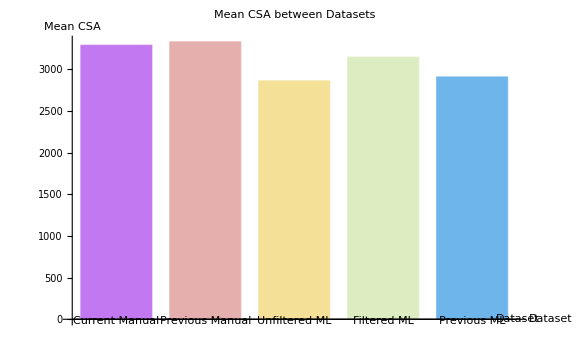

```mathematica
(* mean CSA's for one image*)

(*Calculate the mean CSA for each dataset*)
meanCSA1=Mean[manualASarea[[8]]];
meanCSA2=Mean[manualKSarea[[8]]];
meanCSA3=Mean[unfilteredarea[[8]]];
meanCSA4=Mean[filteredarea[[8]]];
meanCSA5=Mean[mlKSarea[[8]]];


(*Create a bar graph to visualize the mean CSA accuracy*)
BarChart[{meanCSA1,meanCSA2,meanCSA3,meanCSA4,meanCSA5},ChartLabels->{"Current Manual","Previous Manual","Unfiltered ML","Filtered ML","Previous ML"},PlotLabel->"Mean CSA between Datasets",AxesLabel->{"Dataset","Mean CSA"},ImageSize->Large,BarSpacing->Medium,ChartStyle->"Pastel", Background->White, LabelStyle->Directive[Bold,18,Black ]]
```

```mathematica
(******************************************************************************************************************************************)
(*Maybe's*)
(******************************************************************************************************************************************)
```

0.

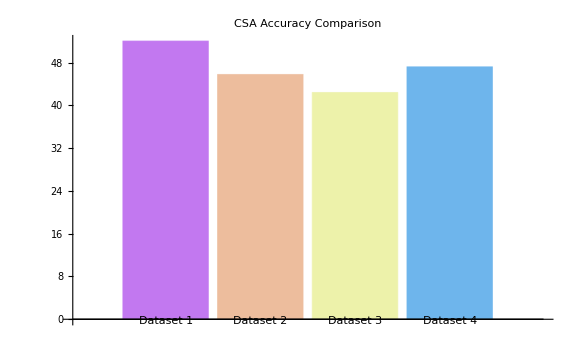

```mathematica
(****check formula****)

(*Calculate CSA accuracy for each dataset compared to the manual dataset*)csaAccuracy[dataset_List,manualDataset_List]:=Mean[Abs[(dataset-manualDataset)/manualDataset]]*100;

(*Find the minimum length among all datasets*)
minLength=Min[Length/@{manualKSarea[[1]],mlKSarea[[1]],filteredarea[[1]],unfilteredarea[[1]]}];

(*Trim all datasets to the minimum length*)
trimmedManual=Take[manualASarea[[1]],minLength];
trimmedDatasets=Take[#,minLength]&/@{manualKSarea[[1]],mlKSarea[[1]],filteredarea[[1]],unfilteredarea[[1]]};

(*Calculate CSA accuracy for each dataset*)
accuracyDataset1=csaAccuracy[trimmedDatasets[[1]],trimmedManual];
accuracyDataset2=csaAccuracy[trimmedDatasets[[2]],trimmedManual];
accuracyDataset3=csaAccuracy[trimmedDatasets[[3]],trimmedManual];
accuracyDataset4=csaAccuracy[trimmedDatasets[[4]],trimmedManual];
accuracyDataset5=csaAccuracy[trimmedManual, trimmedManual]
(*Plot the CSA accuracy values on a bar graph*)
BarChart[{accuracyDataset1,accuracyDataset2,accuracyDataset3,accuracyDataset4},ChartLabels->{"Dataset 1","Dataset 2","Dataset 3","Dataset 4"},ChartStyle->"Pastel",FrameLabel->{"Datasets","CSA Accuracy (%)"},PlotLabel->"CSA Accuracy Comparison",BaseStyle->{FontSize->12,FontFamily->"Arial"},ImageSize->Large]
```

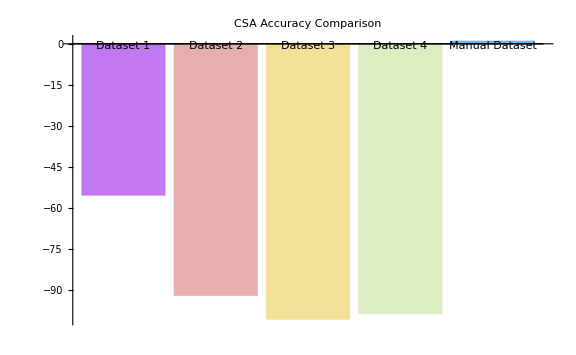

```mathematica
(*Calculate CSA accuracy for each dataset compared to the manual dataset*)csaAccuracy[dataset_List,manualDataset_List]:=(1-Mean[Abs[(dataset-manualDataset)*100/manualDataset]]);

(*Find the minimum length among all datasets*)
minLength=Min[Length/@{manualKSarea[[5]],mlKSarea[[5]],filteredarea[[5]],unfilteredarea[[5]]}];

(*Trim all datasets to the minimum length*)
trimmedManual=Take[manualASarea[[5]],minLength];
trimmedDatasets=Take[#,minLength]&/@{manualKSarea[[5]],mlKSarea[[5]],filteredarea[[5]],unfilteredarea[[5]]};

(*Calculate CSA accuracy for each dataset*)
accuracyDataset1=csaAccuracy[trimmedDatasets[[1]],trimmedManual];
accuracyDataset2=csaAccuracy[trimmedDatasets[[2]],trimmedManual];
accuracyDataset3=csaAccuracy[trimmedDatasets[[3]],trimmedManual];
accuracyDataset4=csaAccuracy[trimmedDatasets[[4]],trimmedManual];
accuracyManual=csaAccuracy[trimmedManual,trimmedManual]; (*Add this line*)

(*Plot the CSA accuracy values on a bar graph*)
BarChart[{accuracyDataset1,accuracyDataset2,accuracyDataset3,accuracyDataset4,accuracyManual},(*Include accuracyManual here*)ChartLabels->{"Dataset 1","Dataset 2","Dataset 3","Dataset 4","Manual Dataset"},(*Add label for manual dataset*)ChartStyle->"Pastel",FrameLabel->{"Datasets","CSA Accuracy (%)"},PlotLabel->"CSA Accuracy Comparison",BaseStyle->{FontSize->12,FontFamily->"Arial"},ImageSize->Large]
```

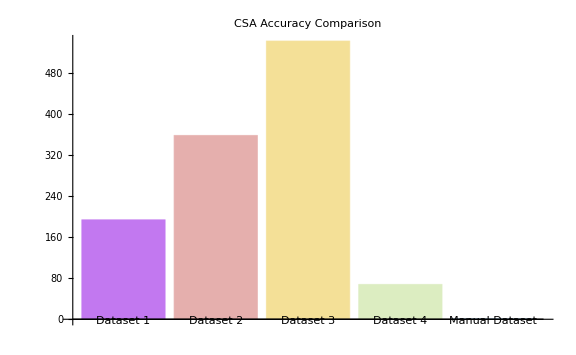

{3195.06,4418.73,3433.74,2340.02,2909.59,3524.84,3137.1,3144.43,3624.02,3688.18,3840.77,2792.14,2863.14,3665.76,2742.,2242.03,2681.12,2527.,2316.06,2043.84,1862.64,1743.9,2167.33,2846.62,2223.06,2169.56}

```mathematica
(*Calculate CSA accuracy for each dataset compared to the manual dataset*)csaAccuracy[dataset_List,manualDataset_List]:=(Total[Abs[(dataset-manualDataset)/manualDataset]*100]);

(*Find the minimum length among all datasets
minLength=Min[Length/@{manualKSarea[[5]],mlKSarea[[5]],filteredarea[[5]],unfilteredarea[[5]]}];

(*Trim all datasets to the minimum length*)
trimmedManual=Take[manualASarea[[5]],minLength];
trimmedDatasets=Take[#,minLength]&/@{manualKSarea[[5]],mlKSarea[[5]],filteredarea[[5]],unfilteredarea[[5]]};*)

(*Calculate CSA accuracy for each dataset*)
accuracyDataset1=csaAccuracy[meanfiltar,meanmanASar];
accuracyDataset2=csaAccuracy[meanunfiltar,meanmanASar];
accuracyDataset3=csaAccuracy[meanmlKSar,meanmanASar];
accuracyDataset4=csaAccuracy[meanmanKSar,meanmanASar];
accuracyManual=csaAccuracy[meanmanASar, meanmanASar]; (*Add this line*)

(*Plot the CSA accuracy values on a bar graph*)
BarChart[{accuracyDataset1,accuracyDataset2,accuracyDataset3,accuracyDataset4,accuracyManual},(*Include accuracyManual here*)ChartLabels->{"Dataset 1","Dataset 2","Dataset 3","Dataset 4","Manual Dataset"},(*Add label for manual dataset*)ChartStyle->"Pastel",FrameLabel->{"Datasets","CSA Accuracy (%)"},PlotLabel->"CSA Accuracy Comparison",BaseStyle->{FontSize->12,FontFamily->"Arial"},ImageSize->Large]

meanfiltar
```

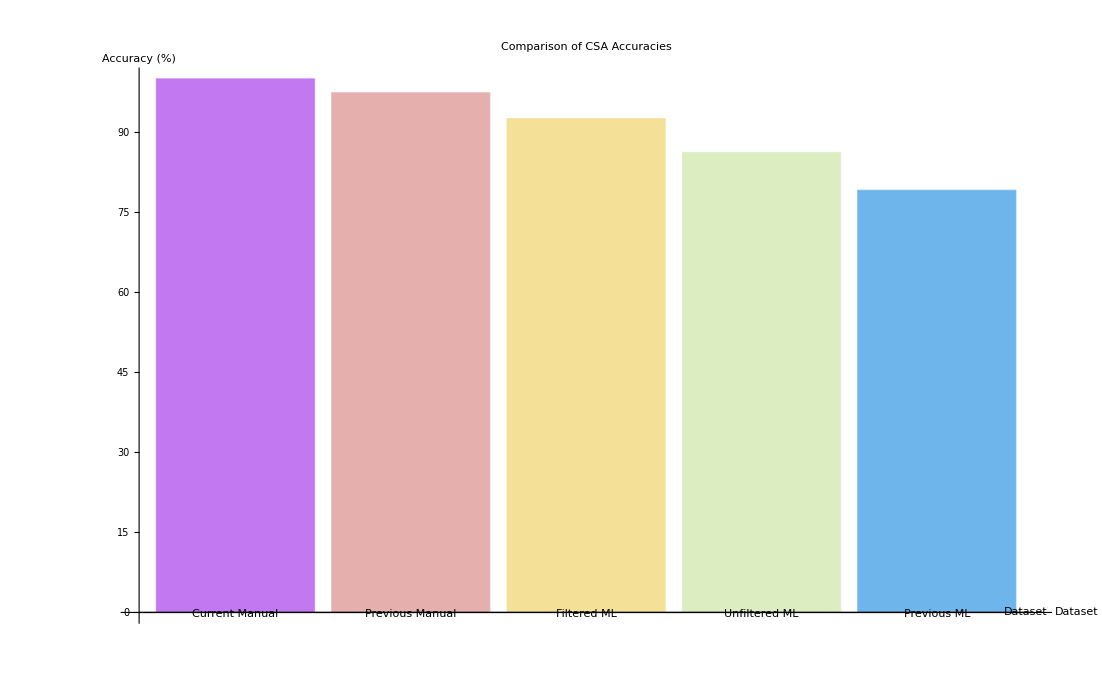

```mathematica
(*Define CSA measurements for each dataset*)


(*Calculate accuracy for each dataset*)
accuracy1=100*Total[1-Abs[(meanmanASar-meanmanKSar)/meanmanASar]]/Length[meanmanASar];
accuracy2=100*Total[1-Abs[(meanmanASar-meanfiltar)/meanmanASar]]/Length[meanmanASar];
accuracy3=100*Total[1-Abs[(meanmanASar-meanunfiltar)/meanmanASar]]/Length[meanmanASar];
accuracy4=100*Total[1-Abs[(meanmanASar-meanmlKSar)/meanmanASar]]/Length[meanmanASar];
accuracy5=100*Total[1-Abs[(meanmanASar-meanmanASar)/meanmanASar]]/Length[meanmanASar];

(*Create a bar chart of accuracy percentages*)
BarChart[{accuracy5,accuracy1,accuracy2,accuracy3,accuracy4},ChartLabels->{"Current Manual","Previous Manual","Filtered ML", "Unfiltered ML", "Previous ML"},ChartStyle->"Pastel",PlotLabel->"Comparison of CSA Accuracies",AxesLabel->{"Dataset","Accuracy (%)"}, Background->White,  LabelStyle->Directive[Bold, Black,22]]
```

```mathematica
meanmanASar
```

{3604.74,4107.28,3626.23,2508.03,3142.68,4000.21,3505.69,3288.22,3686.63,3581.95,3641.37,2651.02,2827.,3675.73,2992.78,2291.67,2227.64,2363.54,1987.57,2145.82,2297.31,1835.96,2128.49,2482.51,2171.28,2411.07}

```mathematica
accuracy1List=Table[100*(1-Abs[(meanmanASar[[i]]-meanmanKSar[[i]])/meanmanASar[[i]]]),{i,Length[meanmanASar]}]
accuracy2List=Table[100*(1-Abs[(meanmanASar[[i]]-meanfiltar[[i]])/meanmanASar[[i]]]),{i,Length[meanmanASar]}]
accuracy3List=Table[100*(1-Abs[(meanmanASar[[i]]-meanunfiltar[[i]])/meanmanASar[[i]]]),{i,Length[meanmanASar]}]
accuracy4List=Table[100*(1-Abs[(meanmanASar[[i]]-meanmlKSar[[i]])/meanmanASar[[i]]]),{i,Length[meanmanASar]}]
accuracy5List=Table[100*(1-Abs[(meanmanASar[[i]]-meanmanASar[[i]])/meanmanASar[[i]]]),{i,Length[meanmanASar]}]

Needs["ANOVA`"]
labeledlist=Flatten[MapIndexed[{First@#2,#1}&,{ accuracy5List, accuracy1List, accuracy2List,accuracy3List, accuracy4List},{2}],1];
anovaModel=ANOVA`ANOVA[labeledlist, PostTests->Bonferroni]
anovaModel=ANOVA`ANOVA[labeledlist, PostTests->Tukey]


tukeysHSD=ResourceFunction["TukeyHSDTest"][anovaModel];

(*To perform Bonferroni correction*)
bonferroniCorrection=ANOVA[anovaModel,PostTests->{"Bonferroni"}];


(*Display the results*)
Multicolumn[{tukeysHSD,bonferroniCorrection},2]
```

{91.4327,98.1409,93.4948,97.3759,95.4409,94.4753,98.4799,98.7717,96.8568,99.7634,90.914,99.7505,99.1348,97.6651,99.4101,99.9179,96.8566,99.309,99.3755,97.371,97.5977,95.8885,99.2314,97.3981,99.1737,98.8592}

{88.635,92.4172,94.6916,93.3012,92.5833,88.1166,89.4859,95.6272,98.3014,97.0343,94.5241,94.677,98.7216,99.729,91.6205,97.8337,79.6429,93.0841,83.4729,95.2474,81.079,94.9859,98.1753,85.3331,97.6154,89.9834}

{76.0874,96.7961,89.2472,86.9704,87.3729,85.9626,85.4169,86.9787,84.8681,91.7647,86.3697,84.6694,90.3336,85.1149,80.9355,81.8601,94.3043,92.9959,97.0491,83.0365,80.1222,84.7011,81.7755,80.6136,85.4577,80.5428}

{78.2478,84.9861,83.1305,83.0683,85.1572,82.7739,84.4279,88.4198,80.5491,83.6823,86.8345,79.8911,83.2151,79.6123,74.1836,76.6601,82.0275,80.8208,76.29,71.2487,75.2355,72.7746,75.6256,72.2171,65.8126,70.215}

{100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.,100.}

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 4 | 7495.34 | 1873.83 | 97.3787 | 1.89933×10^-37
Error | 125 | 2405.34 | 19.2428 |  | 
Total | 129 | 9900.68 |  |  | ,CellMeans→All | 91.0497
Model[1] | 100.
Model[2] | 97.3879
Model[3] | 92.5353
Model[4] | 86.2057
Model[5] | 79.1195,PostTests→{Model→Bonferroni | {{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5}}}}

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 4 | 7495.34 | 1873.83 | 97.3787 | 1.89933×10^-37
Error | 125 | 2405.34 | 19.2428 |  | 
Total | 129 | 9900.68 |  |  | ,CellMeans→All | 91.0497
Model[1] | 100.
Model[2] | 97.3879
Model[3] | 92.5353
Model[4] | 86.2057
Model[5] | 79.1195,PostTests→{Model→Tukey | {{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5}}}}

ResourceObject::notfname: The ResourceObject TukeyHSDTest could not be found.

ANOVA::arg1: The 1st argument has unequal columns or rows.

$Failed[anovaModel] | ANOVA[{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 4 | 7495.34 | 1873.83 | 97.3787 | 1.89933×10^-37
Error | 125 | 2405.34 | 19.2428 |  | 
Total | 129 | 9900.68 |  |  | ,CellMeans→All | 91.0497
Model[1] | 100.
Model[2] | 97.3879
Model[3] | 92.5353
Model[4] | 86.2057
Model[5] | 79.1195,PostTests→{Model→Tukey | {{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5}}}},PostTests→{Bonferroni}]

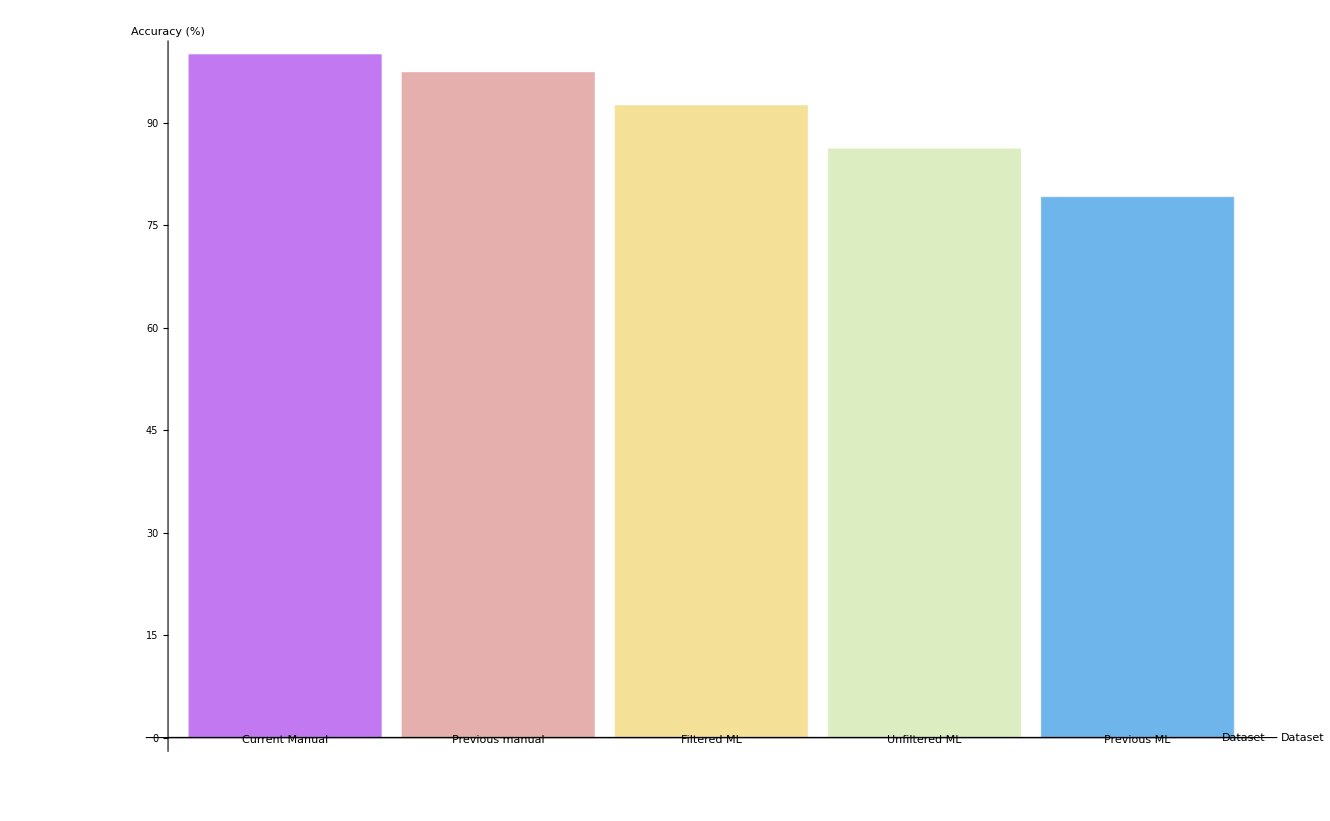

```mathematica
(*Define CSA measurements for each dataset*)


(*Calculate accuracy for each dataset*)
accuracy1=100*Total[1-Abs[(meanmanKSar-meanmanASar)/meanmanASar]]/Length[meanmanASar];
accuracy2=100*Total[1-Abs[(meanfiltar-meanmanASar)/meanmanASar]]/Length[meanmanASar];
accuracy3=100*Total[1-Abs[(meanunfiltar-meanmanASar)/meanmanASar]]/Length[meanmanASar];
accuracy4=100*Total[1-Abs[(meanmlKSar-meanmanASar)/meanmanASar]]/Length[meanmanASar];
accuracy5=100*Total[1-Abs[(meanmanASar-meanmanASar)/meanmanASar]]/Length[meanmanASar];

(*Create a bar chart of accuracy percentages*)
BarChart[{accuracy5,accuracy1,accuracy2,accuracy3,accuracy4},ChartLabels->{"Current Manual","Previous manual","Filtered ML", "Unfiltered ML", "Previous ML"},ChartStyle->"Pastel",AxesLabel->{"Dataset","Accuracy (%)"}, Background->White,  LabelStyle->Directive[Bold, Black,18]]
```

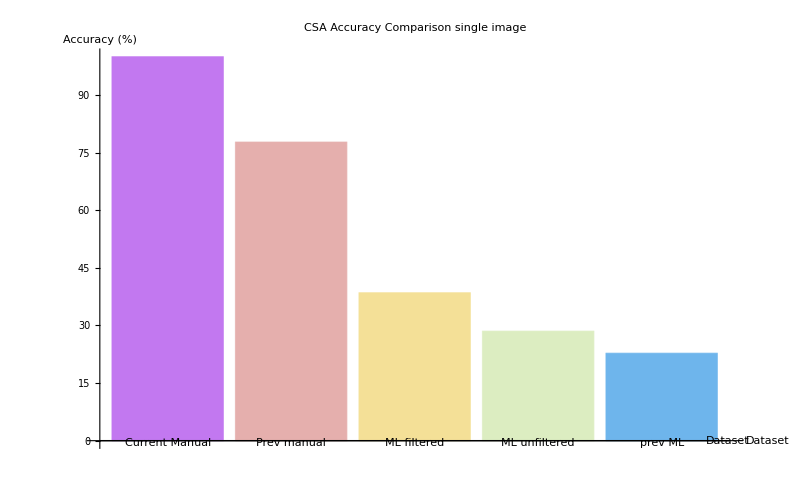

```mathematica
(*Define CSA measurements for each dataset*)

minLength=Min[Length/@{manualKSarea[[18]],mlKSarea[[18]],filteredarea[[18]],unfilteredarea[[18]]}];

(*Trim all datasets to the minimum length*)
trimmedManual=Take[manualASarea[[18]],minLength];
trimmedDatasets=Take[#,minLength]&/@{manualKSarea[[18]],mlKSarea[[18]],filteredarea[[18]],unfilteredarea[[18]]};
(*Calculate accuracy for each dataset*)
accuracy1=100*Total[1-Abs[(trimmedManual-trimmedDatasets[[1]])/trimmedManual]]/Length[trimmedManual];
accuracy2=100*Total[1-Abs[(trimmedManual-trimmedDatasets[[2]])/trimmedManual]]/Length[trimmedManual];
accuracy3=100*Total[1-Abs[(trimmedManual-trimmedDatasets[[3]])/trimmedManual]]/Length[trimmedManual];
accuracy4=100*Total[1-Abs[(trimmedManual-trimmedDatasets[[4]])/trimmedManual]]/Length[trimmedManual];
accuracy5=100*Total[1-Abs[(trimmedManual-trimmedManual)/trimmedManual]]/Length[trimmedManual];

(*Create a bar chart of accuracy percentages*)
BarChart[{accuracy5,accuracy1,accuracy2,accuracy3,accuracy4},ChartLabels->{"Current Manual","Prev manual","ML filtered", "ML unfiltered", "prev ML"},ChartStyle->"Pastel",PlotLabel->"CSA Accuracy Comparison single image",AxesLabel->{"Dataset","Accuracy (%)"}, Background->White,  LabelStyle->Directive[Bold, Black,18]]
```

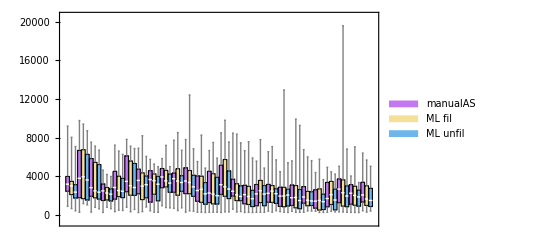

```mathematica
(*comparing roundness for manual AS, Manual KS and ML unifltered*)
combinedData=Transpose[{manualASarea, filteredarea,unfilteredarea}];

(*Create the stacked box-and-whisker chart*)
BoxWhiskerChart[combinedData,ChartStyle->{EdgeForm[Black],"Pastel"},Background->White, ChartLegends->{"manualAS", "ML fil", "ML unfil"}]
```